```mathematica
Print["SaveFigures: ",SetterBar[Dynamic[SaveFigures],{True->"On",False->"Off"}]]
```

SaveFigures:  |

## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
Clear[SaveFigures];

KPImport[file_String,opts___]:=Module[{},
If[AbsoluteTime[FileDate[file]]<AbsoluteTime[{2013,3,7}],
Print[Style["Warning: File "<>file<>" is older than March 7, 2012!",FontColor->Red]];
];
Return[Import[file,opts]];
];
```

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## Combined analysis

### 3+1 fit

```mathematica
DataFiles="~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"lsnd","mb200-all-full","lsnd-mbapp","evid","nevid","nevid-app","nevid-disapp","app","disapp"};

MyContours={χ2[2,0.1],χ2[2,0.01]};
MyStyles={
{Directive[Thick,Black],Directive[Thick,Black,Dashed]},
{Directive[Thick,RGBColor[0,0.5,0]],Directive[Thick,RGBColor[0,0.5,0],Dashed]},
{{Directive[Black],Directive[Black,Dashed]},{GrayLevel[0.7],Red,None}},

{{Directive[Black],Directive[Black,Dashed]},{GrayLevel[0.7],Red,None}},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,RGBColor[0,0.5,0]],Directive[Thick,RGBColor[0,0.5,0],Dashed]},
{Directive[Thick,Black],Directive[Thick,Black,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}
};

(* Apperance experiments *)
DataFiles="~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-"<>#<>".dat.gz"&/@{"lsnd","mb200-nu-app-full","mb200-nubar-app-full","e776","e776-reactors","karmen","nomad","icarus","mb200-combi-app-full"}; 
AppendTo[DataFiles,"~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41th14th24-app.dat.gz"];
DataFiles=Join[DataFiles,"3-3p1/icecube-meeting/dm41thmeUm4-"<>#<>".dat.gz"&/@{"icarus-2014","opera-2013"}];
ExpLabels={"LSND","MiniBooNE ν","MiniBooNE ν̄","E776","E776+LBL reactors","KARMEN","NOMAD","ICARUS 2012","MB Combi","all app.","ICARUS 2014","OPERA"};
MyStyles={Directive[Thick,#],Directive[Thick,#,Dotted]}&/@{Directive[RGBColor[.6,0,0]],Directive[Black],Directive[Orange,Dashed],RGBColor[0,.6,0],RGBColor[0,.6,0],Directive[Blue,Dotted],RGBColor[.4,.4,1],RGBColor[1,0,1],Black,Red,Directive[RGBColor[1,0,1],Thickness[0.01],Dashing[{0.03,0.01}]],Directive[RGBColor[.6,0,.6],Thickness[0.01],Dashing[{0.03,0.01}]]};

(* ICARUS *)
(*DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"icarus"}; 
ExpLabels={"ICARUS"};
MyStyles={Directive[Thick,#],Directive[Thick,#,Dashed]}&/@{RGBColor[1,0,1]};*)

(* Results from Pedro's MiniBooNE code *)
(*DataFiles="3-3p1/dm41thmeUm4-mb200-"<>#<>".dat.gz"&/@{"combi-app","combi-app-full","combi-disapp","combi-disapp-full","all","all-full"};
MyLabels={"app","app (full osc.)","disapp","disapp (full osc.)","app+disapp","app+disapp (full osc)"};
MyStyles={Directive[Thick,#],Directive[Thick,#,Dashed]}&/@{Directive[Thickness[Medium],Red],Directive[Thickness[Medium],Orange],Directive[Thick,RGBColor[.6,0,0]],Directive[Thickness[Medium],Blue],Directive[Thickness[Medium],Magenta],Directive[Thick,RGBColor[0,0,.6]]};*)

ThetaEffMuE[th14_,th24_]:=Module[{Ue4,Uμ4},
Ue4=Sin[th14];
Uμ4=Cos[th14]*Sin[th24];
Return[4.Abs[Ue4]^2Abs[Uμ4]^2];
];
For[i=1,i≤Length[DataFiles],i++,
(* If the data has already been reduced to dmsq-theff form load processed data set *)
ProcessedFile[i]=StringDrop[DataFiles⟦i⟧,-3]<>".processed";
If[FileExistsQ[ProcessedFile[i]]&&OrderedQ[{FileDate[DataFiles⟦i⟧],FileDate[ProcessedFile[i]]}],
DataFiles=ReplacePart[DataFiles,i->ProcessedFile[i]];
];

Print["Processing ",DataFiles⟦i⟧,"..."];
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[Sqrt[10^#⟦2⟧]/10^#⟦3⟧>1,1.*^12,#⟦4⟧]}&/@Data[i];
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i],

(* Else - data files in dm41, th14, th24 *)
logth14Min[i]=Min[Data[i]⟦All,2⟧];
logth14Max[i]=Max[Data[i]⟦All,2⟧];
logth24Min[i]=Min[Data[i]⟦All,3⟧];
logth24Max[i]=Max[Data[i]⟦All,3⟧];
Data[i]=Sort[{#⟦1⟧,Log10[ThetaEffMuE[10^#⟦2⟧,10^#⟦3⟧]],#⟦4⟧}&/@Data[i]];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
logs22thMin[i]=Min[Data[i]⟦All,2⟧];
logs22thMax[i]=Max[Data[i]⟦All,2⟧];

(* Extract best fit point: Either it has been computed accurate, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

(*i=8;
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Off[FindMinimum::reged,FindMinimum::lstol];
{Chi2Min[i],BFP[i]}=FindMinimum[DataInterpol[i][p1,p2],{p1,BFP[i]⟦1⟧,logdmsqMin[i],logdmsqMax[i]},{p2,BFP[i]⟦2⟧,logs22thMin[i],logs22thMax[i]}]/.Rule[s_,x_]:>x;
On[FindMinimum::reged,FindMinimum::lstol];*)
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],logs22thMin[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-lsnd.dat.gz...

Best fit: sin^22θ_μe=0.00939595, Δm^2=3.54813

χ_min^2=5.79326, χ_(no osc)^2=50.3981, Δχ_(no osc.)^2=44.6048 (CL 1.)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-mb200-nu-app-full.dat.gz...

Best fit: sin^22θ_μe=0.00194984, Δm^2=3.16228

χ_min^2=13.8393, χ_(no osc)^2=20.9507, Δχ_(no osc.)^2=7.11141 (CL 0.971439)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-mb200-nubar-app-full.dat.gz...

Best fit: sin^22θ_μe=0.616595, Δm^2=0.0501187

χ_min^2=9.61207, χ_(no osc)^2=19.5331, Δχ_(no osc.)^2=9.92108 (CL 0.992991)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-e776.dat.gz...

Best fit: sin^22θ_μe=0.00245471, Δm^2=10

χ_min^2=23.7801, χ_(no osc)^2=31.0809, Δχ_(no osc.)^2=7.30078 (CL 0.974019)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-e776-reactors.dat.gz...

Best fit: sin^22θ_μe=0.0000977237, Δm^2=5.01187

χ_min^2=61.1177, χ_(no osc)^2=63.3875, Δχ_(no osc.)^2=2.26987 (CL 0.678558)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-karmen.dat.gz...

Best fit: sin^22θ_μe=0.000489779, Δm^2=6.30957

χ_min^2=6.80423, χ_(no osc)^2=6.87339, Δχ_(no osc.)^2=0.0691633 (CL 0.0339905)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-nomad.dat.gz...

Best fit: sin^22θ_μe=0.0000977237, Δm^2=0.0158489

χ_min^2=2.53859×10^-13, χ_(no osc)^2=2.53859×10^-13, Δχ_(no osc.)^2=0. (CL 0)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-icarus.dat.gz...

Best fit: sin^22θ_μe=0.000489779, Δm^2=0.0158489

χ_min^2=0.290955, χ_(no osc)^2=0.3154, Δχ_(no osc.)^2=0.0244454 (CL 0.0121483)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41thmeUm4-mb200-combi-app-full.dat.gz...

Best fit: sin^22θ_μe=0.616595, Δm^2=0.0501187

χ_min^2=29.4274, χ_(no osc)^2=46.9551, Δχ_(no osc.)^2=17.5278 (CL 0.999844)

Processing ~/olymp/papers/2013/sterile-nu/sim/3-3p1/dm41th14th24-app.dat.gz...

Best fit: sin^22θ_μe=0.0123027, Δm^2=0.446684

χ_min^2=88.3591, χ_(no osc)^2=135.613, Δχ_(no osc.)^2=47.2541 (CL 1.)

Processing 3-3p1/icecube-meeting/dm41thmeUm4-icarus-2014.dat.gz...

Best fit: sin^22θ_μe=0.000389045, Δm^2=0.0158489

χ_min^2=0.657434, χ_(no osc)^2=0.701766, Δχ_(no osc.)^2=0.0443321 (CL 0.0219222)

Processing 3-3p1/icecube-meeting/dm41thmeUm4-opera-2013.dat.gz...

Best fit: sin^22θ_μe=0.00154882, Δm^2=0.0158489

χ_min^2=0.304989, χ_(no osc)^2=0.352924, Δχ_(no osc.)^2=0.0479346 (CL 0.0236824)

```mathematica
(* Data in response to Jon Link's email from 2013-03-27 *)
(*Export["../for-jon/dm41-s22thme-allapp.dat",Data[10]];*)
```

```mathematica
(* Use a more sophisticated conversion from Subscript[θ, 14], Subscript[θ, 24] for those experiments which are sensitive to both of them independently.
We use: x=sin 2 Subscript[θ, 14], c = sin 2 Subscript[θ, eff] = sin 2 Subscript[θ, 14] sin Subscript[θ, 24] => Subscript[θ, 24] = arcsin(c/x), Subscript[θ, 14] = 0.5 arcsin x *)
Clear[x,j];
For[i=1,i≤Length[DataFiles],i++,
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
Continue[];
];
If[!StringMatchQ[DataFiles⟦i⟧,RegularExpression[".*(evid|app|minos|e776).*"]],
Continue[];
];
If[StringMatchQ[DataFiles⟦i⟧,RegularExpression[".*\\.processed"]],
Continue[];
];
Print["Processing ",DataFiles⟦i⟧,"..."];
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
DataInterpolFull[i]=Interpolation[Data[i],InterpolationOrder->1];

MinFunc[i][logdmsq_?NumericQ,logs22th_?NumericQ,x_?NumericQ]:=Module[{},DataInterpolFull[i][logdmsq,Clip[Log10[0.5ArcSin[x]],{logth14Min[i],logth14Max[i]}],Clip[Log10[ArcSin[Clip[Sqrt[10^logs22th]/x,{0,1}]]],{logth24Min[i],logth24Max[i]}]]
];
DataInterpol[i]=(FindMinimum[MinFunc[j][#1,#2,x],{x,Sort[Table[{MinFunc[i][-0.4,-1,x],x},{x,Sqrt[10^#2],0.99999,0.025}]]⟦1,2⟧,Sqrt[10^#2],0.99999}]⟦1⟧&)/.{j->i};

Off[FindMinimum::lstol];
DataProcessed[i]=Flatten[Table[N[{logdmsq,Log10[ArcSin[Sqrt[10^logs22th]]/2],Log10[π/2],t=DataInterpol[i][logdmsq,logs22th],t}],{logdmsq,logdmsqMin[i],logdmsqMax[i]+1*^-10,(logdmsqMax[i]-logdmsqMin[i])/(Length[Union[Data[i]⟦All,1⟧]]-1)},{logs22th,-4,-0.2,0.1}],1];
If[Abs[Chi2Min[i]-Min[DataProcessed[i]⟦All,-1⟧]]>0.1,
Print["Warning: Global χ^2 minimum not contained in processed data table!"];
AppendTo[DataProcessed[i],"Chi2Min = "<>ToString[Chi2Min[i]]];
];
On[Clip::ncompl,FindMinimum::lstol];
Export[ProcessedFile[i],DataProcessed[i],"Table"];
];
```

```mathematica
For[i=1,i≤Length[DataFiles],i++,
If[Head[MyStyles⟦i,1⟧]===List,
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->MyStyles⟦i,2⟧,ContourStyle->MyStyles⟦i,1⟧],
(* Else *)
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles⟦i⟧]
];
];
```

#### Quality of the appearance fit

Run above code to load data from appearance experiments, then run the following

```mathematica
(* Compute χ^2 at best fit value for appearance fit *)
(* Note: Minor discreoancies expected due to hierarchies, different marginalized parameters, etc. *)
Print[10^BFP[Length[DataFiles]]⟦1;;2⟧];
For[i=1,i≤Length[DataFiles],i++,
Print[ExpLabels⟦i⟧,": ",DataInterpol[i][BFP[Length[DataFiles]]⟦1⟧,BFP[Length[DataFiles]]⟦2⟧]];
];
```

{0.0158489,0.00154882}

LSND: 50.3865

MiniBooNE ν: 20.9459

MiniBooNE ν̄: 19.5278

E776: 31.081

E776+LBL reactors: 63.3877

KARMEN: 6.87373

NOMAD: 6.37666×10^-11

ICARUS 2012: 0.350118

MB Combi: 46.9457

InterpolatingFunction::dmval: Input value TraditionalForm`{-1.8, -2.81} lies outside the range of data in the interpolating function. Extrapolation will be used.

all app.: 135.951

ICARUS 2014: 0.74893

OPERA: 0.304989

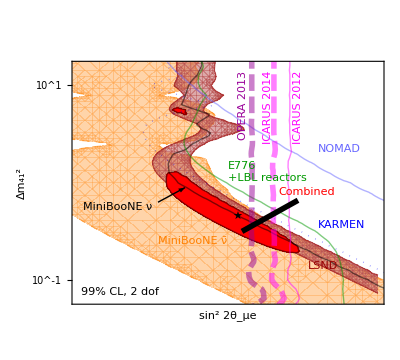

```mathematica
MyLegend=Framed[Grid[
Table[{LegendLine[MyStyles⟦i,1⟧],ExpLabels⟦i⟧},{i,{1,2,3,5,6,7,8}}],
Alignment->Left,BaseStyle->{FontSize->12}],Background->RGBColor[1,1,1,.7]];
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-4,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.01]},ContourShading->If[i==10,{Directive[MyStyles⟦i,1⟧],None},If[i==1||i==3,{Directive[Lighter[MyStyles⟦i,1,2,1⟧],Opacity[0.5]],None},None]],ContourStyle->If[i==10,Black,MyStyles⟦i,1⟧]]
];
Show[MyPlot[3],MyPlot[1],MyPlot[10],MyPlot[2],MyPlot[5],MyPlot[6],MyPlot[7],MyPlot[8],MyPlot[11],MyPlot[12],PlotRange->{{-3.5,-0.5},{-1.2,1.2}},FrameLabel->{"sin^2 2θ_μe","Δm_41^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{Style[{
(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Black,Text["★",BFP[10]⟦{2,1}⟧],
MyStyles⟦1,1⟧,Text["LSND",{-1.2,-0.8},{-1,1},{1,-0.55}],
MyStyles⟦2,1⟧,Text[Style["MiniBooNE ν"(*,Background->GrayLevel[1,.7]*)],{-3.45,-0.2},{-1,1},{1,0}],
Dashing[{}],Thickness[Medium],Arrow[{{-2.7,-0.2},{-2.43,-0.05}}],
MyStyles⟦3,1⟧,Text["MiniBooNE ν̄",{-2.7,-0.55},{-1,1},{1,-0.6}],
MyStyles⟦5,1⟧,Text[Style["E776\n\!\(\*StyleBox[\"+LBL reactors\",FontSize->13]\)",LineSpacing->{0.8,0},TextAlignment->Left,Background->GrayLevel[1,.7]],{-2.0,0},{-1,-1}],
MyStyles⟦6,1⟧,Text["KARMEN",{-1.1,-0.38},{-1,1},{1,-0.55}],
MyStyles⟦7,1⟧,Text["NOMAD",{-1.1,0.4},{-1,1},{1,-0.6}],
MyStyles⟦8,1⟧,Text["ICARUS 2012",{-1.35,1.15},{1,1},{0,1}],
MyStyles⟦11,1⟧,Text["ICARUS 2014",{-1.55,1.15},{1,-1},{0,1},Background->GrayLevel[1,.7]],
MyStyles⟦12,1⟧,Text["OPERA 2013",{-1.8,1.15},{1,-1},{0,1},Background->GrayLevel[1,.7]],
MyStyles⟦10,1⟧,Text[Style["Combined",Background->GrayLevel[1,.7]],{-1.5,-0.1},{-1,0}],
Black,Dashing[{}],Thickness[Medium],Arrow[{{-1.3,-0.18},BFP[Length[DataFiles]-2]⟦{2,1}⟧+{0.05,-0.15}}],
Black,Text["99% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]
},FontSize->16]},DisplayFunction->JHEPPlot]
```

#### E776

Run above code to load E776 data file, then run the following

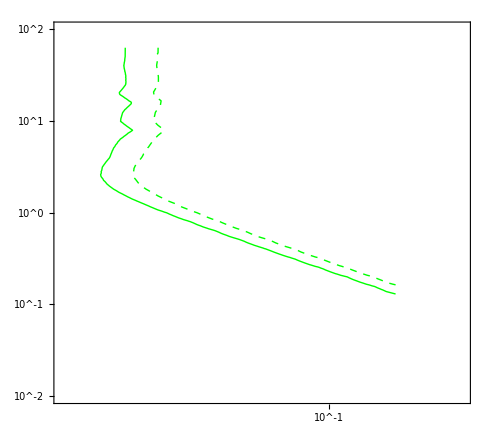

```mathematica
(* NOTE: E776 reference: http://dx.doi.org/10.1103/PhysRevLett.68.274 *)
Show[MyPlot[1]/.Black->Green,
PlotRange->{{-3,0},{-2,2}},ImageSize->490,AspectRatio->.9,ImagePadding->{{140,15},{70,25}},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},Prolog->{Inset[Import["0-code/glb/e776/data/E776-binned.pdf"]⟦1⟧,Scaled[{.44,.45}]]}]
```

31.0815

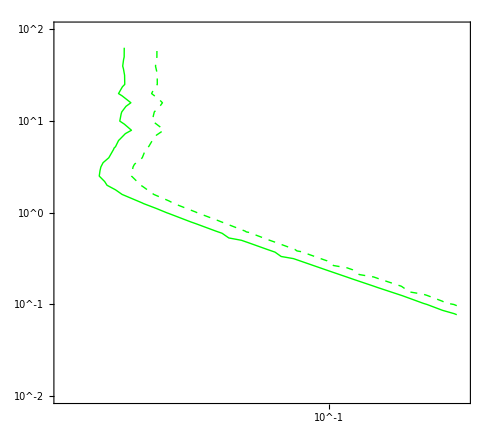

```mathematica
MyData=Cases[Import["3-3p1/e776-2flavor.dat.gz"],{Repeated[_?NumericQ]}];
Min[MyData⟦All,3⟧]
Show[ListContourPlot[{Log10[Sin[2 10^#⟦2⟧]^2],#⟦1⟧,Min[#⟦3⟧,#⟦4⟧]}&/@MyData,Contours->%+MyContours,ContourShading->False,ContourStyle->MyStyles⟦1⟧/.Black:>Green],
PlotRange->{{-3,0},{-2,2}},ImageSize->490,AspectRatio->.9,ImagePadding->{{140,15},{70,25}},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},Prolog->{Inset[Import["0-code/glb/e776/data/E776-binned.pdf"]⟦1⟧,Scaled[{.44,.45}]]}]
```

673.751

ListContourPlot::gmat: {{-3., -1.8, 673.751}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{-3.,-1.8,673.751}},Contours→{678.356,682.961},PlotRange→Full,ContourShading→False,ContourStyle→GrayLevel[0]]

28.8302

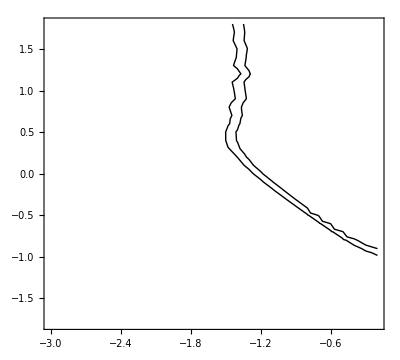

```mathematica
MyData=Import["0-code/glb/e776/pedro/E776chi.dat"];
Min[MyData⟦All,3⟧]
ListContourPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧],#⟦3⟧}&/@MyData,Contours->%+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Black]

MyData=Cases[Import["3-3p1/dm41th14th24-e776-test.dat.gz"],{Repeated[_?NumericQ]}];
Min[MyData⟦All,3⟧]
ListContourPlot[{#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@MyData,Contours->%+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Black]
```

#### Icarus

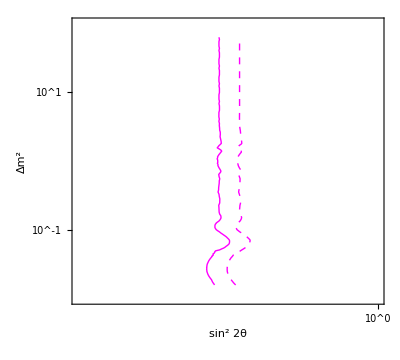

```mathematica
Show[MyPlot[1],
PlotRange->{{-3,0},{-2,2}},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]}]
```

```mathematica
Chi2Min[1]
```

0.366271

```mathematica
i=1;
Data[i]=Cases[KPImport["3-3p1/delta0delta1-icarus-test2.dat.gz"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1⟧,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
```

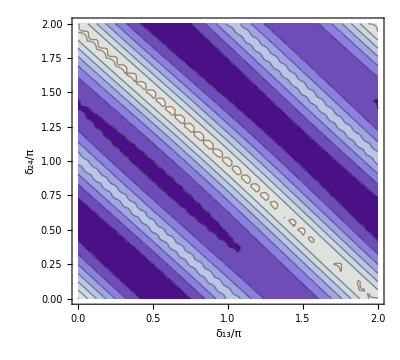

```mathematica
ContourPlot[DataInterpol[i][δ0*π,δ1*π],{δ0,0,2},{δ1,0,2},FrameLabel->{"δ_13/π","δ_24/π"}]
```

#### MINOS phase dependence

```mathematica
i=1;
Data[i]=Cases[KPImport["3-3p1/delta0delta1-minos-test2.dat.gz"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1⟧,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
```

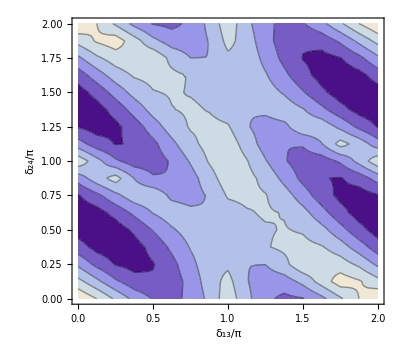

```mathematica
ContourPlot[DataInterpol[i][δ0*π,δ1*π],{δ0,0,2},{δ1,0,2},FrameLabel->{"δ_13/π","δ_24/π"}]
```

#### Pedro’s MiniBooNE code - 2-flavor fit

```mathematica
i=1;
DataFiles={"3-3p1/mb200-2f.dat","3-3p1/mb475-2f.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Log10[Sin[2 10^#⟦2⟧]^2],#⟦1⟧,#⟦3⟧}&/@Cases[Import[DataFiles⟦i⟧],{Repeated[_?NumericQ]}];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
```

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListContourPlot[Data[i],Contours->Chi2Min[i]+{1000,750,500,300,100,50,30,20,17,15,χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]},PlotRange->{{-3.5,Full},Full,All},ContourShading->False,ContourStyle->Directive[Thick,Black],FrameLabel->{"sin^22θ_μe","Δm_41^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]}]
];
```

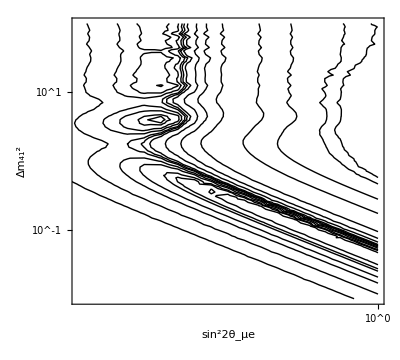

```mathematica
MyPlot[1]
```

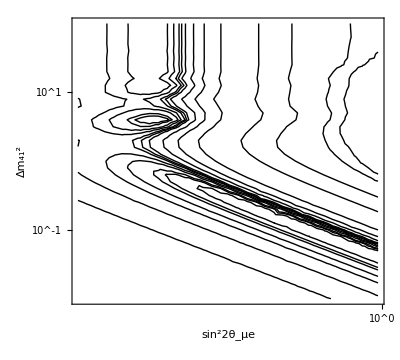

```mathematica
(* The following plot has been obtained before Pedro Oct 2012 optimizations (fewer L and E bins, lower filter_sigma, etc. *)
MyPlot[1]
```

```mathematica
Chi2Min[1]
```

105.749

#### Pedro’s MiniBooNE code - Full fit

For the following, uncomment corresponding code under “Appearance experiments and 3+1 fit” and run first 3 cells.

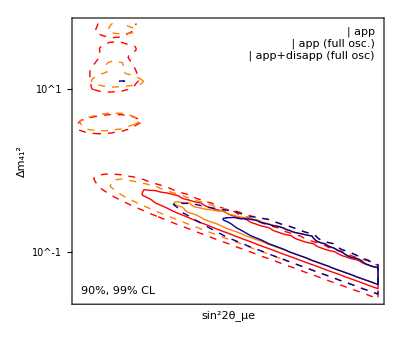

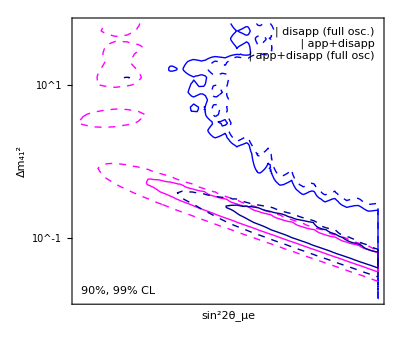

```mathematica
MyLegend=Framed[Grid[
Table[{LegendLine[MyStyles⟦j,1⟧],MyLabels⟦j⟧},{j,{1,2,6}}],
Alignment->Left,BaseStyle->{FontSize->20},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]];
MyCombinedPlot=Show[MyPlot[1],MyPlot[2],MyPlot[6],FrameLabel->{"sin^22θ_μe","Δm_41^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{Text[Style["90%, 99% CL"],Scaled[{0.03,0.03}],{-1,-1}],
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}
]
MyLegend=Framed[Grid[
Table[{LegendLine[MyStyles⟦j,1⟧],MyLabels⟦j⟧},{j,4,6}],
Alignment->Left,BaseStyle->{FontSize->20},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]];
MyCombinedPlot=Show[MyPlot[4],MyPlot[5],MyPlot[6],FrameLabel->{"sin^22θ_μe","Δm_41^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{Text[Style["90%, 99% CL"],Scaled[{0.03,0.03}],{-1,-1}],
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}
]
```

#### Atmospheric neutrinos

```mathematica
(* ATM *)
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"atm"}; 
For[i=1,i≤Length[DataFiles],i++,
Print["Reading "<>DataFiles⟦i⟧<>" ..."];
Data[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Log10[Sin[10^#⟦2⟧]^2],Log10[(Cos[10^#⟦2⟧]Sin[10^#⟦3⟧])^2],#⟦1⟧,Min[#⟦{-2,-1}⟧]}&/@N[Data[i]];
Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
(*Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i,2]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i,3]={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];*)

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i,1]=Interpolation[Data[i,1],InterpolationOrder->1];
(*DataInterpol[i,2]=Interpolation[Data[i,2],InterpolationOrder->1];
DataInterpol[i,3]=Interpolation[Data[i,3],InterpolationOrder->1];*)

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];
p3Min[i]=Min[Data[i]⟦All,3⟧];
p3Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
Chi2Min[i]=BFPoint[i]⟦-1⟧;
(*Off[FindMinimum::reged,FindMinimum::lstol];
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2,p3],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]},{p3,BFPoint[i]⟦3⟧,p3Min[i],p3Max[i]}]/.Rule[s_,x_]:>x;
On[FindMinimum::reged,FindMinimum::lstol];
Print["Best fit: sin^2θ_24=",10^BFPoint[i]⟦1⟧,", Δm^2=",10^BFPoint[i]⟦2⟧,", sin^2θ_23=",BFPoint[i]⟦3⟧];
Chi2NoOsc[i]=DataInterpol[i][p1Min[i],p2Min[i],p3Min[i]];
Print["χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];*)
];
```

Reading 3-3p1/dm41th14th24-atm.dat.gz ...

InterpolatingFunction::dmval: Input value {-7.99946, -8.1852} lies outside the range of data in the interpolating function. Extrapolation will be used.

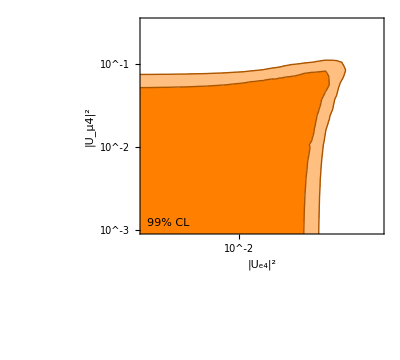

```mathematica
i=1;
ContourPlot[DataInterpol[i,1][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Contours->{χ2[2,0.1],χ2[2,0.01]},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},PlotRange->{{-3,-0.5},{-3,-0.5},All},ContourStyle->Darker[Orange],ContourShading->{Orange,Lighter[Orange,.5],None},FrameTicks->{LogTicks[-4,1],LogTicks[-4,4],LogTicksNoLabel[-4,1],LogTicksNoLabel[-4,4]},
Epilog->{Text["★",BFPoint[i]⟦{1,2}⟧],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.7]]}]
```

#### Global fits

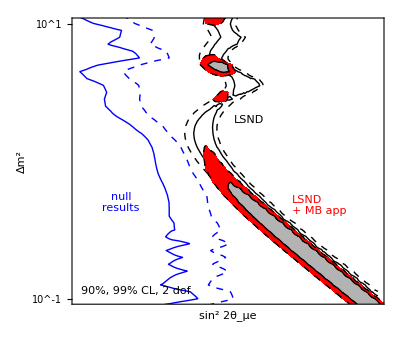

```mathematica
MyCombinedPlot=Show[MyPlot[1],(*MyPlot[2],*)MyPlot[3],MyPlot[5],PlotRange->{{-4.0,-0.5},{-1,1}},FrameLabel->{"sin^2 2θ_μe","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{
MyStyles⟦1,1⟧,Text["LSND",{-2,0.3}],
(*MyStyles⟦2,1⟧,Text["MB",{-1.9,-0.8}],*)
MyStyles⟦5,1⟧,Text[Style["null\nresults",LineSpacing->{1,0}],{-3.5,-0.3}],
Red,Text[Style["LSND\n+ MB app",LineSpacing->{1,0}],{-1.5,-0.4},{-1,-1}],
Black,Text["90%, 99% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]
},DisplayFunction->JHEPPlot]
If[SaveFigures,
Export["fig/3p1-lsndmb-vs-rest.eps",MyCombinedPlot];
];
```

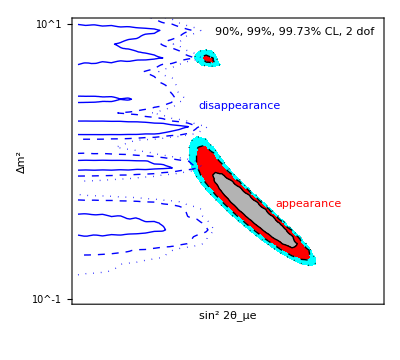

```mathematica
i=8;
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-4,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.1],χ2[2,0.01],χ2[2,PValue[3]]},ContourShading->{GrayLevel[0.7],Red,Cyan,None},ContourStyle->(Directive[Black,#]&/@{Dashing[{}],Dashed,Dotted})];
i=9;
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-4,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.1],χ2[2,0.01],χ2[2,PValue[3]]},ContourShading->False,ContourStyle->(Directive[Thick,Blue,#]&/@{Dashing[{}],Dashed,Dotted})];
MyCombinedPlot=Show[MyPlot[8],MyPlot[9],PlotRange->{{-4,-0.5},{-1,1}},FrameLabel->{"sin^2 2θ_μe","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{
MyStyles⟦9,1⟧,Text["disappearance",{-2.6,.4},{-1,0}],
Red,Text["appearance",{-1.7,-0.35},{-1,-1},{1,-0.7}],
Black,Text["90%, 99%, 99.73% CL, 2 dof",Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,0.7]]
},DisplayFunction->JHEPPlot]
If[SaveFigures,
Export["fig/3p1-appdisapp.eps",MyCombinedPlot];
];
```

ContourPlot::plln: Limiting value Max[-4, Min[-4.01, {0.9} ⟦ -2 ⟧]] in {logth, Max[-4, logs22thMin[i]], logs22thMax[i]} is not a machine-sized real number.

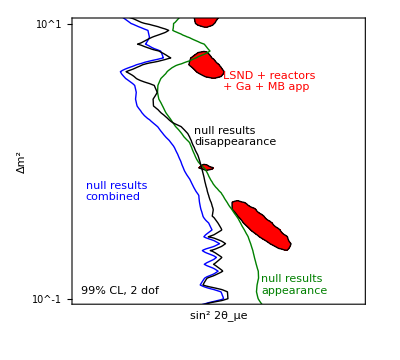

```mathematica
For[i=1,i≤Length[DataFiles],i++,
If[Head[MyStyles⟦i,1⟧]===List,
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-4,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.01]},ContourShading->MyStyles⟦i,2,{2,3}⟧,ContourStyle->MyStyles⟦i,1,1⟧],
(* Else *)
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-4,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.01]},ContourShading->False,ContourStyle->MyStyles⟦i,1⟧]
];
]
MyCombinedPlot=Show[MyPlot[4],MyPlot[5],MyPlot[6],MyPlot[7],PlotRange->{{-4.0,-0.5},{-1,1}},FrameLabel->{"sin^2 2θ_μe","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{
Red,Text[Style["LSND + reactors \n+ Ga + MB app",LineSpacing->{1,0}],{-2.2,0.5},{-1,-1}],
MyStyles⟦6,1⟧,Text[Style["null results\nappearance",LineSpacing->{1,0}],{-1.72,-0.98},{-1,-1}],
MyStyles⟦7,1⟧,Text[Style["null results\ndisappearance",LineSpacing->{1,0}],{-2.55,0.1},{-1,-1}],
MyStyles⟦5,1⟧,Text[Style["null results\ncombined",LineSpacing->{1,0}],{-3.9,-0.3},{-1,-1}],
Black,Text["99% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]
},DisplayFunction->JHEPPlot]
If[SaveFigures,
Export["fig/3p1-evid-nevid.eps",MyCombinedPlot];
];
```

### Individual disappearance experiments

```mathematica
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"sbl","karmen-c12","karmen-c12-JR","lsnd-c12","c12"};
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"reactors-all-except-kaml","reactors-sbl","reactors-sbl-bugeysp"};
(*DataFiles={"7-3flavor/solar-test.dat.gz"};*)
ThetaEffEE[th14_]:=Sin[2th14]^2;
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]={#⟦1,1⟧,Log10[ThetaEffEE[10^#⟦1,2⟧]],Min[#⟦All,-1⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logthMin[i]=Min[Data[i]⟦All,2⟧];
logthMax[i]=Max[Data[i]⟦All,2⟧];
];
```

```mathematica
MyStyles={Directive[Thick,Red],Directive[Thick,Red,Dashed],Directive[Thick,Red,Dotted]};
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01]};
For[i=1,i≤Length[DataFiles],i++,
MyPlotLog[i]=
ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{-3.5,-0.5},{-2,2},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50];
MyPlotLinear[i]=ContourPlot[DataInterpol[i][logdmsq,Log10[th]]-Chi2Min[i],{th,10^logthMin[i],10^logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{0,1},{-1,2},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,GridLines->Automatic,PlotPoints->50];
];
```

#### Experiments with Thomas' reactor code

Load appropriate data file and run code above, then run the following

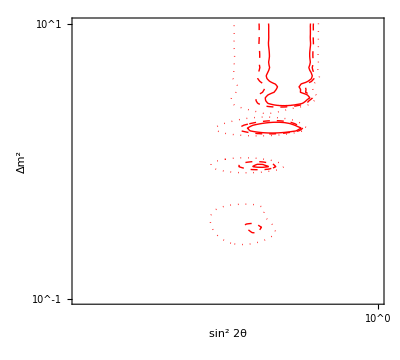

```mathematica
Show[MyPlotLog[1],FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},PlotRange->{{-3,0},{-1,1}}]
```

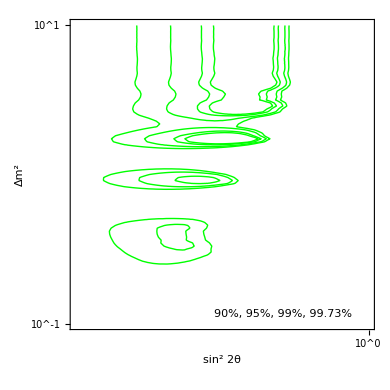

```mathematica
(* The following was done with the pre-Nu2012 version of Thomas' code *)
i=1;
MyPlot[1]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,0.0027]},ContourShading->False,ContourStyle->Directive[Green],PlotRange->{{-2,0},{-1,1},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50,Epilog->{Text["90%, 95%, 99%, 99.73%",Scaled[{0.7,0.05}]]},Prolog->{Inset[Import["0-code/reactors/figs/react-3p1.pdf"]⟦1⟧,Scaled[{.64,.48}]]},ImageSize->390,AspectRatio->1]
```

```mathematica
i=1;
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,0.0027]};
ThomasData=Cases[Import["0-code/reactors/thomas/sbl_bugey.dat","Table"],{Repeated[_?NumericQ]}];
Show[
ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->Directive[Green],PlotRange->{{-2,0},{-1,1},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50,Epilog->{Text["90%, 95%, 99%, 99.73%",Scaled[{0.7,0.05}]]}],
ListContourPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧],#⟦3⟧}&/@ThomasData,PlotRange->All,Contours->Min[ThomasData⟦All,3⟧]+MyContours,ContourShading->False,ContourStyle->Black]
]
```

-Graphics-

```mathematica
DataFiles="3-3p1/th13th14-"<>#<>".dat.gz"&/@{"reactors-all-except-kaml","reactors-lbl","reactors-sbl-bugeysp"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Log10[Sin[2 10^#⟦1⟧]^2],Log10[Sin[2 10^#⟦2⟧]^2],Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
logs22th13Min[i]=Min[Data[i]⟦All,1⟧];
logs22th13Max[i]=Max[Data[i]⟦All,1⟧];
logs22th14Min[i]=Min[Data[i]⟦All,2⟧];
logs22th14Max[i]=Max[Data[i]⟦All,2⟧];

MyPlot[i]=ContourPlot[DataInterpol[i][logs22th13,logs22th14]-Chi2Min[i],{logs22th13,logs22th13Min[i],logs22th13Max[i]},{logs22th14,logs22th14Min[i],logs22th14Max[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{-1.5,-0.5},{-2,0},All},FrameLabel->{"sin^2 2θ_13","sin^2 2θ_14"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50];
];
```

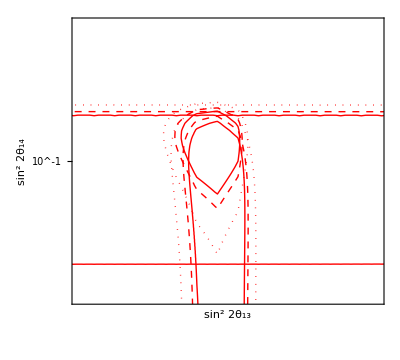

```mathematica
Show[MyPlot[3],MyPlot[2],MyPlot[1]]
```

#### Experiments with Michele's solar neutrino code

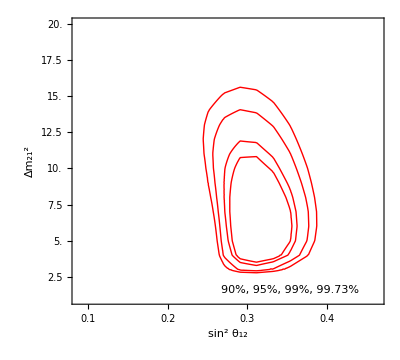

```mathematica
DataFiles={"7-3flavor/solar.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
dmsqMin[i]=Min[Data[i]⟦All,2⟧];
dmsqMax[i]=Max[Data[i]⟦All,2⟧];
sthMin[i]=Min[Data[i]⟦All,1⟧];
sthMax[i]=Max[Data[i]⟦All,1⟧];
];
i=1;
MyPlot[1]=ContourPlot[DataInterpol[i][sth,dmsq*1*^-5]-Chi2Min[i],{sth,sthMin[i],sthMax[i]},{dmsq,dmsqMin[i]/1*^-5,dmsqMax[i]/1*^-5},Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,0.0027]},ContourShading->False,ContourStyle->Directive[Red,Thick],PlotRange->Full,FrameLabel->{"sin^2 θ_12","Δm_21^2"},DisplayFunction->JHEPPlot,PlotPoints->50,Epilog->{Text["90%, 95%, 99%, 99.73%",Scaled[{0.7,0.05}]]}]
```

#### Experiments with Pedro’s SBL codes

Load appropriate data file and run code above, then run the following

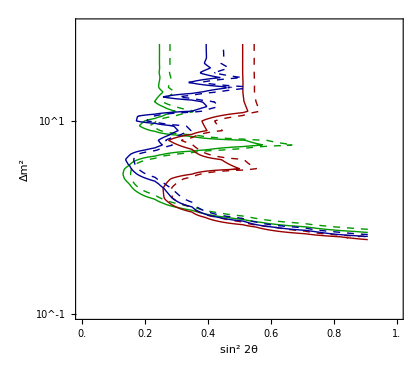

```mathematica
i=2;
j=4;
k=5;
MyStyles={Directive[Thick,RGBColor[0,.6,0]],Directive[Thick,RGBColor[0,.6,0],Dashed],Directive[Thick,RGBColor[0,.6,0],Dotted]};
MyContours={χ2[2,0.1],χ2[2,0.05]};
Show[
ContourPlot[DataInterpol[i][logdmsq,Log10[th]]-Chi2Min[i],{th,10^logthMin[i],10^logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{0,1},{-1,2},All},PlotPoints->50],
ContourPlot[DataInterpol[j][logdmsq,Log10[th]]-Chi2Min[j],{th,10^logthMin[j],10^logthMax[j]},{logdmsq,logdmsqMin[j],logdmsqMax[j]},Contours->MyContours,ContourShading->False,ContourStyle->(MyStyles/.RGBColor[___]:>RGBColor[0.6,0,0]),PlotRange->{{0,1},{-1,2},All},PlotPoints->50],
ContourPlot[DataInterpol[k][logdmsq,Log10[th]]-Chi2Min[k],{th,10^logthMin[k],10^logthMax[k]},{logdmsq,logdmsqMin[k],logdmsqMax[k]},Contours->MyContours,ContourShading->False,ContourStyle->(MyStyles/.RGBColor[___]:>RGBColor[0,0,0.6]),PlotRange->{{0,1},{-1,2},All},PlotPoints->50],
Prolog->{Inset[Import["0-code/glb/c12/data/nue-carbon-analysis.pdf"]⟦1⟧,Scaled[{.44,.48}]]},
FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,ImageSize->420,AspectRatio->0.9]
```

0.551275

3.81441

34.1748

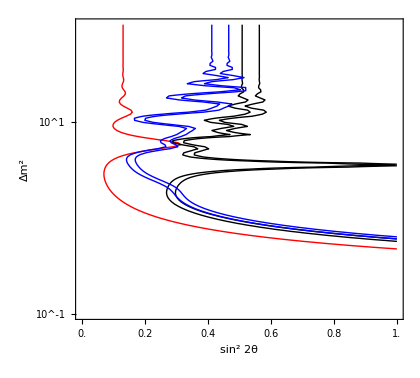

```mathematica
(* KARMEN - reproducing JR's analysis with Pedro's code, + LSND + Combi *)
Clear[MyData];
MyData[1]=Import["0-code/glb/c12/pedro-separate/KM-chi.dat"];
MyData[2]=Import["0-code/glb/c12/pedro-separate/LS-chi.dat"];
MyData[3]=Import["0-code/glb/c12/pedro-combined/comb-chi.dat"];
Min[MyData[1]⟦All,3⟧]
Min[MyData[2]⟦All,3⟧]
Min[MyData[3]⟦All,3⟧]
Show[
ListContourPlot[{#⟦2⟧,Log10[#⟦1⟧],#⟦3⟧}&/@MyData[1],Contours->{1.28},PlotRange->Full,ContourShading->False,ContourStyle->Red],
ListContourPlot[{#⟦2⟧,Log10[#⟦1⟧],#⟦3⟧}&/@MyData[2],Contours->Min[MyData[2]⟦All,3⟧]+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Black],
ListContourPlot[{#⟦1⟧,Log10[#⟦2⟧],#⟦3⟧}&/@MyData[3],Contours->Min[MyData[3]⟦All,3⟧]+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Blue],
FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,Prolog->{Inset[Import["0-code/glb/c12/data/preliminary-karmen-nue-carbon-JR.pdf"]⟦1⟧,Scaled[{.44,.48}]]},ImageSize->420,AspectRatio->0.9]
```

0.303905

3.81466

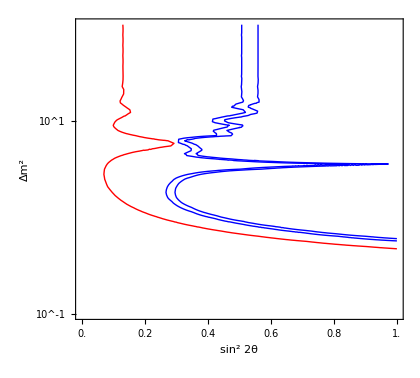

```mathematica
(* KARMEN - reproducing JR's analysis with a 2 flavor fit *)
Clear[MyData];
DataFiles="3-3p1/"<>#<>".dat.gz"&/@{"karmen-c12-2flavor-JR","lsnd-c12-2flavor"};
For[i=1,i≤Length[DataFiles],i++,
MyData[i]=Cases[Import[DataFiles⟦i⟧],{Repeated[_?NumericQ]}];
MyData[i]={Sin[2 10^#⟦2⟧]^2,#⟦1⟧,Min[#⟦3⟧,#⟦4⟧]}&/@MyData[i];
MyDataInterpol[i]=Interpolation[MyData[i],InterpolationOrder->1];
];
Min[MyData[1]⟦All,3⟧]
Min[MyData[2]⟦All,3⟧]
Show[
ContourPlot[MyDataInterpol[1][s22th,logdm],{s22th,0,1},{logdm,-1,2},Contours->{χ2[1,0.2]},PlotRange->Full,ContourShading->False,ContourStyle->Red],
ContourPlot[MyDataInterpol[2][s22th,logdm],{s22th,0,1},{logdm,-1,2},Contours->Min[MyData[2]⟦All,3⟧]+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Blue],
FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,Prolog->{Inset[Import["0-code/glb/c12/data/preliminary-karmen-nue-carbon-JR.pdf"]⟦1⟧,Scaled[{.44,.48}]]},ImageSize->420,AspectRatio->0.9]
```

#### MiniBooNE disappearance analysis

```mathematica
DataFiles="3-3p1/dm41thmeUm4-mb200-"<>#<>".dat.gz"&/@{"nu-disapp","nubar-disapp","nu-disapp-full","nubar-disapp-full"};
MyLabels={"ν_μ disapp","(ν̄)_μ disapp","ν_μ disapp (full osc.)","(ν̄)_μ disapp (full osc.)"};
MyStyles={Directive[Thick,#],Directive[Thick,#,Dashed]}&/@{Directive[Thickness[Medium],Gray],Directive[Thickness[Medium],Orange],Black,Red};

For[i=1,i≤Length[DataFiles],i++,
Print["Processing ",DataFiles⟦i⟧,"..."];
DataRaw[i]=Import[DataFiles⟦i⟧,"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]={#⟦1⟧,#⟦3⟧,#⟦2⟧,If[Sqrt[10^#⟦2⟧]/10^#⟦3⟧>1,1.*^12,#⟦4⟧]}&/@Data[i]; (* NOTE: Flip order! *)
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i],

(* Else - data files in dm41, th14, th24 *)
Print["WRONG FILE FORMAT!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
logUm4Min[i]=Min[Data[i]⟦All,2⟧];
logUm4Max[i]=Max[Data[i]⟦All,2⟧];

Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
];
```

Processing 3-3p1/dm41thmeUm4-mb200-nu-disapp.dat.gz...

Processing 3-3p1/dm41thmeUm4-mb200-nubar-disapp.dat.gz...

Processing 3-3p1/dm41thmeUm4-mb200-nu-disapp-full.dat.gz...

Processing 3-3p1/dm41thmeUm4-mb200-nubar-disapp-full.dat.gz...

```mathematica
For[i=1,i≤Length[DataFiles],i++,
If[Head[MyStyles⟦i,1⟧]===List,
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,(log4Um4sq-Log10[4.])/2]-Chi2Min[i],{log4Um4sq,Max[-4,2logUm4Min[i]+Log10[4.]],2logUm4Max[i]+Log10[4.]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->MyStyles⟦i,2⟧,ContourStyle->MyStyles⟦i,1⟧],
(* Else *)
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,(log4Um4sq-Log10[4.])/2]-Chi2Min[i],{log4Um4sq,Max[-4,2logUm4Min[i]+Log10[4.]],2logUm4Max[i]+Log10[4.]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles⟦i⟧]
];
];
```

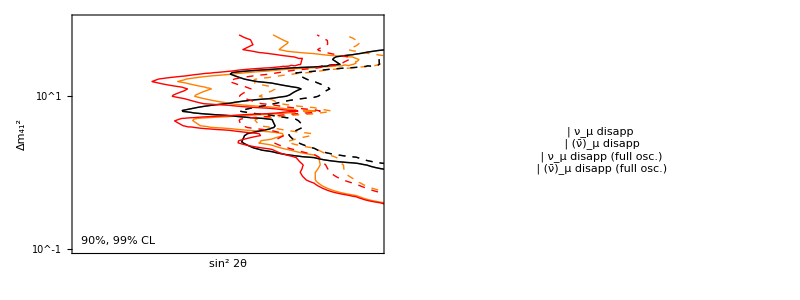

```mathematica
MyLegend=Framed[Grid[
Table[{LegendLine[MyStyles⟦j,1⟧],MyLabels⟦j⟧},{j,1,Length[MyLabels]}]
,Alignment->Left,BaseStyle->{FontSize->20},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]];
MyCombinedPlot=Show[MyPlot[1],MyPlot[2],MyPlot[3],MyPlot[4],PlotRange->{{-1.7,-0.3},{-1,2}},FrameLabel->{"sin^2 2θ","Δm_41^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{Text[Style["90%, 99% CL"],Scaled[{0.03,0.03}],{-1,-1}]}
];
MyGridPlot=Grid[{{MyCombinedPlot,Graphics[Inset[MyLegend],ImageSize->{250}]}},Spacings->0]
If[SaveFigures,
Export["fig/mb-disapp.eps",MyGridPlot];
];
```

### 3+1 fit - θ_14 vs. θ_24 vs. Δm_41^2

```mathematica
(*DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"mb200-combi-app","mb200-combi-app-full","disapp-e","disapp-mu"};*)
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"atm"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1⟧,Log10[Sin[2 10^#⟦2⟧]^2],Log10[Sin[2 10^#⟦3⟧]^2],Min[#⟦{-2,-1}⟧]}&/@Data[i];
Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i,2]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i,3]={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i,1]=Interpolation[Data[i,1],InterpolationOrder->1];
DataInterpol[i,2]=Interpolation[Data[i,2],InterpolationOrder->1];
DataInterpol[i,3]=Interpolation[Data[i,3],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];
p3Min[i]=Min[Data[i]⟦All,3⟧];
p3Max[i]=Max[Data[i]⟦All,3⟧];

p2Min[i]=-2;
p3Min[i]=-2;

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2,p3],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]},{p3,BFPoint[i]⟦3⟧,p3Min[i],p3Max[i]}]/.Rule[s_,x_]:>x;
];
```

Warning: File 3-3p1/dm41th14th24-atm.dat.gz is older than Feb 7, 2012!

FindMinimum::streg: The starting point {-1.8, -7.39794, -7.39794} is not in the search region {{-1.8, -2., -2.}, {1.8, -0.0421112, -0.0421112}}.

Set::shape: Lists {Chi2Min[i], BFPoint[i]} and FindMinimum[DataInterpol[i][p1, p2, p3], {p1, BFPoint[i] ⟦ 1 ⟧, p1Min[i], p1Max[i]}, {p2, BFPoint[i] ⟦ 2 ⟧, p2Min[i], p2Max[i]}, {p3, BFPoint[i] ⟦ 3 ⟧, p3Min[i], p3Max[i]}] are not the same shape.

FindMinimum::streg: The starting point {-1.8, -7.39794, -7.39794} is not in the search region {{-1.8, -2., -2.}, {1.8, -0.0421112, -0.0421112}}.

General::stop: Further output of FindMinimum :: streg will be suppressed during this calculation.

```mathematica
MyStyles={
{{Directive[Thick,Blue],Directive[Thick,Dashed,Blue],Directive[Thick,Dotted,Blue]},None},
{Directive[Thick,Blue,Dashed],None},
{Directive[Thick,Orange,DotDashed],None},
{Directive[Thick,Black,Dotted],None}
};
MyLegend=Framed[Grid[{
{LegendLine[MyStyles⟦1,1⟧],"MB app"},
{LegendLine[MyStyles⟦2,1⟧],"MB app full"},
{LegendLine[MyStyles⟦3,1⟧],"ν_e disapp"},
{LegendLine[MyStyles⟦4,1⟧],"ν_μ disapp"}
},Alignment->Left,BaseStyle->{FontSize->12},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]];
For[i=1,i≤Length[DataFiles],i++,
MyOptions={PlotRange->Full,Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01]},ContourShading->MyStyles⟦i,2⟧,ContourStyle->MyStyles⟦i,1⟧,ImagePadding->{{100,10},{70,10}}};
MyPlot[i,1]=ContourPlot[DataInterpol[i,1][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Δm_41^2 [eV^2]","Sin^2 2θ_14"},FrameTicks->{LogTicks[-4,4],LogTicks[-4,1],LogTicksNoLabel[-4,1],LogTicksNoLabel[-4,4]},
Epilog->{Text["★",BFPoint[i]⟦{1,2}⟧],
Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}]}];
MyPlot[i,2]=ContourPlot[DataInterpol[i,2][p1,p3]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p3,p3Min[i],p3Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Δm_41^2 [eV^2]","Sin^2 2θ_24"},FrameTicks->{LogTicks[-4,4],LogTicks[-4,1],LogTicksNoLabel[-4,4],LogTicksNoLabel[-4,1]},
Epilog->{Text["★",BFPoint[i]⟦{1,3}⟧],
Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}]}];
MyPlot[i,3]=ContourPlot[DataInterpol[i,3][p2,p3]-Chi2Min[i],{p3,p3Min[i],p3Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 2θ_24","Sin^2 2θ_14"},FrameTicks->{LogTicks[-4,1],LogTicks[-4,1],LogTicksNoLabel[-4,1],LogTicksNoLabel[-4,1]},
Epilog->{Text["★",BFPoint[i]⟦{3,2}⟧],Text["90%, 95%, 99%",Scaled[{0.97,0.03}],{1,-1}]}];
];
Clear[MyCombinedPlot];
For[j=1,j≤3,j++,
MyCombinedPlot[j]=Show[Sequence@@Table[MyPlot[i,j],{i,Length[DataFiles],1,-1}]]
];
Grid[{{Show[MyCombinedPlot[2]]},
{Show[MyCombinedPlot[1]],Show[MyCombinedPlot[3]]}}]
```

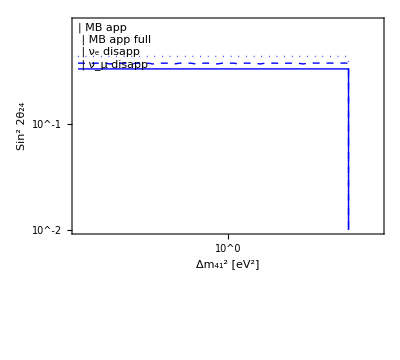
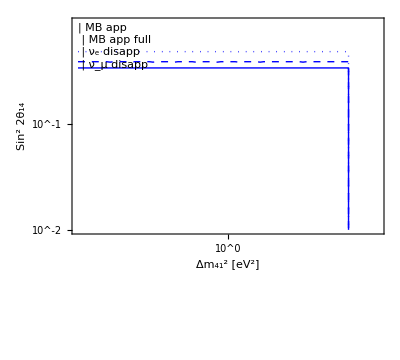
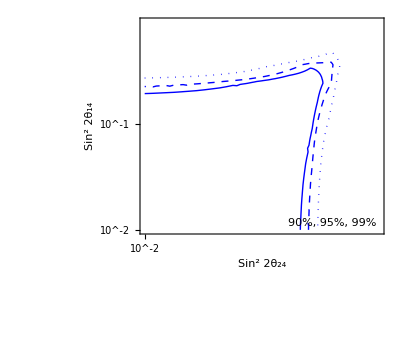

### ν_e disappearance analysis - θ_13 vs. θ_14 vs. Δm_41^2

```mathematica
DataFiles="3-3p1/dm41th13th14-"<>#<>".dat.gz"&/@{"gal","sblreactors",(*"disapp-e",*)"lblreactors","c12",(*"solar-kaml",*)"gal"(*,"sbllblreactors"*)};
For[i=1,i≤Length[DataFiles],i++,
Print["Reading ",DataFiles⟦i⟧,"..."];
Data[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Log10[Max[1*^-4,Sin[#⟦3⟧]^2]],#⟦1⟧,Sin[2#⟦2⟧]^2,Min[#⟦{-2,-1}⟧]}&/@Data[i];
Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i,2]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i,3]={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i,1]=Interpolation[Data[i,1],InterpolationOrder->1];
DataInterpol[i,2]=Interpolation[Data[i,2],InterpolationOrder->1];
DataInterpol[i,3]=Interpolation[Data[i,3],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];
p3Min[i]=Min[Data[i]⟦All,3⟧];
p3Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
Off[FindMinimum::reged,FindMinimum::lstol];
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2,p3],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]},{p3,BFPoint[i]⟦3⟧,p3Min[i],p3Max[i]}]/.Rule[s_,x_]:>x;
On[FindMinimum::reged,FindMinimum::lstol];
Print["Best fit: sin^22θ_14=",Sin[2*ArcSin[Sqrt[10^BFPoint[i]⟦1⟧]]]^2,", Δm^2=",10^BFPoint[i]⟦2⟧,", sin^22θ_13=",BFPoint[i]⟦3⟧];
Off[InterpolatingFunction::dmval,FindMinValue::lstol];
Chi2NoOsc[i]=FindMinValue[DataInterpol[i][p1Min[i],p2Min[i],p3],{p3,0.1}];
On[InterpolatingFunction::dmval,FindMinValue::lstol];
Print["χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
];
```

Reading 3-3p1/dm41th13th14-gal.dat.gz...

Best fit: sin^22θ_14=0.318821, Δm^2=2.23872, sin^22θ_13=0.318821

FindMinValue::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

χ_min^2=2.0514, χ_(no osc)^2=10.9827, Δχ_(no osc.)^2=8.93131 (CL 0.988503)

Reading 3-3p1/dm41th13th14-sblreactors.dat.gz...

Best fit: sin^22θ_14=0.0873322, Δm^2=1.77828, sin^22θ_13=0.0320516

χ_min^2=58.6314, χ_(no osc)^2=67.3583, Δχ_(no osc.)^2=8.72691 (CL 0.987266)

Reading 3-3p1/dm41th13th14-lblreactors.dat.gz...

Best fit: sin^22θ_14=0.00039996, Δm^2=0.0398107, sin^22θ_13=0.0873322

χ_min^2=94.8767, χ_(no osc)^2=94.8767, Δχ_(no osc.)^2=0.0000224894 (CL 0.0000112447)

Reading 3-3p1/dm41th13th14-c12.dat.gz...

Best fit: sin^22θ_14=0.0873322, Δm^2=7.94328, sin^22θ_13=0.

InterpolatingFunction::dprec: The precision of input value {-4, -1.4, 3.07597×10^15} and/or the interpolation grid is insufficient to compute the value.

FindMinValue::nrnum: The function value TagBox[InterpolatingFunction[{{-4.`, -0.4964529131387181`}, {-1.4`, 1.4`}, {0.`, 0.31882112276166324`}}, {5, 7, 0, {21, 57, 11}, {2, 2, 2}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {Developer`PackedArrayForm, {« 1 »}, {34.72997228`, 34.72997213`, 34.7299717`, 34.72997098`, 34.72996999`, 34.72996874`, 34.72996725`, 34.72996554`, 34.72996364`, 34.72996157`, 34.72995936`, « 29 », 34.72996554`, 34.72996364`, 34.72996157`, 34.72995936`, 34.72997228`, 34.72997213`, 34.7299717`, 34.72997098`, 34.72996999`, 34.72996874`, « 13117 »}}, {Automatic, Automatic, Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] is not a real number at {p3} = {3.07597×10^15}.

χ_min^2=34.1918, χ_(no osc)^2=-1.47707×10^10, Δχ_(no osc.)^2=-1.47707×10^10 (CL 0)

Reading 3-3p1/dm41th13th14-gal.dat.gz...

Best fit: sin^22θ_14=0.318821, Δm^2=2.23872, sin^22θ_13=0.318821

FindMinValue::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

χ_min^2=2.0514, χ_(no osc)^2=10.9827, Δχ_(no osc.)^2=8.93131 (CL 0.988503)

Reading results/dm41th13th14-daya-bay.dat...

Best fit: sin^22θ_14=0.0873322, Δm^2=0.00125893, sin^22θ_13=0.0873322

FindMinValue::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinValue :: fmgz will be suppressed during this calculation.

χ_min^2=22.316, χ_(no osc)^2=30.211, Δχ_(no osc.)^2=7.89495 (CL 0.980697)

```mathematica
(* Data in response to Jon Link's email from 2013-03-27 *)
(*Export["../for-jon/Ue4sq-dm41-gal.dat",Data[1,1]];
Export["../for-jon/Ue4sq-dm41-sbl-reactors.dat",Data[2,1]];
Export["../for-jon/Ue4sq-dm41-disapp-e.dat",Data[3,1]];*)
```

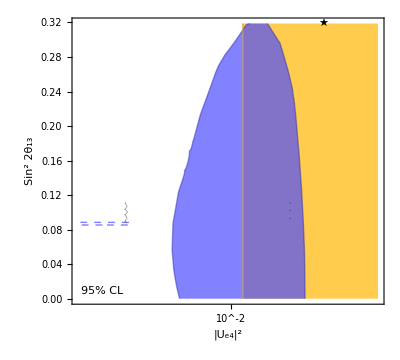
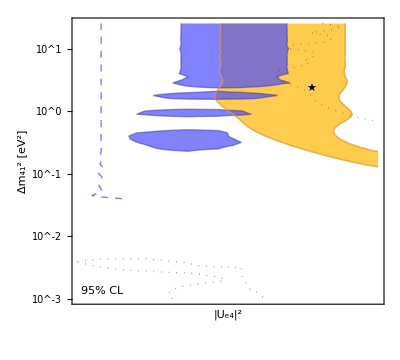
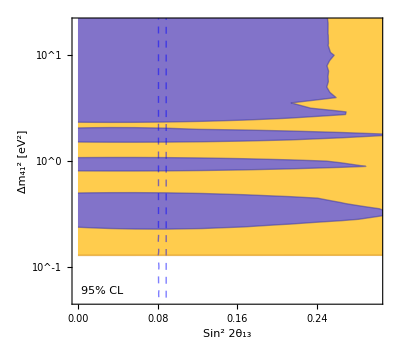
-Graphics- | 
-Graphics- | -Graphics-

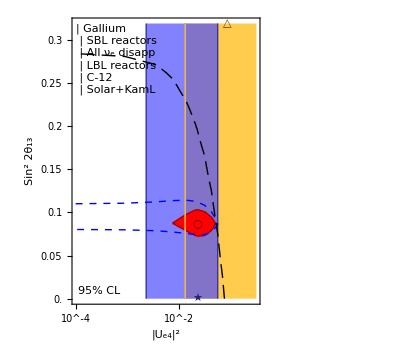
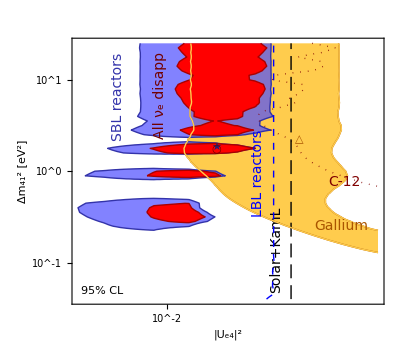
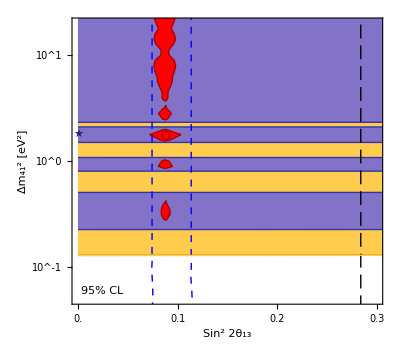
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
MyStyles={
{Darker[Orange],{Directive[RGBColor[1,.8,.3],Opacity[1]],None}},
{Darker[RGBColor[.3,.3,1]],{Directive[RGBColor[.3,.3,1],Opacity[0.7]],None}},
(*{Darker[Red],{Directive[Red,Opacity[1]],None}},*)
{Directive[Thick,Blue,Dashed],None},
{Directive[Thick,RGBColor[0.5,0,0],Dotted],None},
(*{Directive[Thick,Black,AbsoluteDashing[{10,5}]],None},*)
{Directive[Thick,RGBColor[1,.8,.3]],None},
{Directive[Thick,Black,Dotted],None}
};
MyLegend=Framed[Grid[{
(*{LegendBox[MyStyles⟦1,2,1⟧,None,"△",Darker[MyStyles⟦1,1⟧]],"Gallium"},
{LegendBox[MyStyles⟦2,2,1⟧,None,"★",Darker[MyStyles⟦2,1⟧]],"SBL reactors"},
{LegendBox[MyStyles⟦3,2,1⟧,None,"○",Darker[MyStyles⟦3,1⟧]],Style["All ν_e disapp",TextAlignment->Left,LineSpacing->{1,0}]},
{LegendLine[MyStyles⟦4,1⟧],"LBL reactors"},
{LegendLine[MyStyles⟦5,1⟧],"C-12"},
{LegendLine[MyStyles⟦6,1⟧],"Solar+KamL"}*)
},Alignment->Left,BaseStyle->{FontSize->12},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.8]];
For[i=1,i≤Length[DataFiles],i++,
MyOptions={PlotRange->Full,Contours->{χ2[2,0.05]},ContourShading->MyStyles⟦i,2⟧,ContourStyle->MyStyles⟦i,1⟧,ImagePadding->{{100,10},{70,10}}};
MyPlot[i,1]=ContourPlot[DataInterpol[i,1][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"|U_e4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-4,4],LogTicks[-4,4]},{LogTicksNoLabel[-4,4],LogTicksNoLabel[-4,4]}},
Epilog->{Text["★",BFPoint[i]⟦{1,2}⟧],
Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}]}];
MyPlot[i,2]=ContourPlot[DataInterpol[i,2][p1,p3]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p3,p3Min[i],p3Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"|U_e4|^2","Sin^2 2θ_13"},FrameTicks->{{Automatic,Automatic},{LogTicks[-4,1],LogTicksNoLabel[-4,1]}},
Epilog->{Text["★",BFPoint[i]⟦{1,3}⟧],
Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}]}];
MyPlot[i,3]=ContourPlot[DataInterpol[i,3][p2,p3]-Chi2Min[i],{p3,p3Min[i],p3Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 2θ_13","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-4,4],LogTicksNoLabel[-4,4]},{Automatic,Automatic}},
Epilog->{Text["★",BFPoint[i]⟦{3,2}⟧],
Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]]}];

(* Fixed Subscript[Δm, 41]^2 plots *)
dmsqTable={Log10[10.],BFPoint[3]⟦2⟧};
For[k=1,k≤Length[dmsqTable],k++,
Chi2MinLocal[i,20+k]=NMinimize[{DataInterpol[i][p1,dmsqTable⟦k⟧,p3],p1Min[i]≤p1≤p1Max[i]&&p3Min[i]≤p3≤p3Max[i]},{p1,p3}]⟦1⟧;
MyPlot[i,20+k]=ContourPlot[DataInterpol[i][p1,dmsqTable⟦k⟧,p3]-Chi2MinLocal[i,20+k],{p1,p1Min[i],p1Max[i]},{p3,p3Min[i],p3Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"|U_e4|^2","Sin^2 2θ_13"},FrameTicks->{{Automatic,Automatic},{LogTicks[-4,1],LogTicksNoLabel[-4,1]}},
Epilog->{Text["★",BFPoint[i]⟦{1,3}⟧],
Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
Text["Δm_41^2 = "<>ToString[Round[10^dmsqTable⟦k⟧,0.01]]<>" eV^2",Scaled[{0.97,0.03}],{1,-1},Background->GrayLevel[1,0.8]],
Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}]}];
]; (* For[k] *)
]; (* For[i] *)

Clear[MyCombinedPlot];
For[j=1,j≤3,j++,
(*MyCombinedPlot[j]=JHEPPlot[Show[Sequence@@Table[cleanContourPlot[MyPlot[i,j]],{i,1,Length[DataFiles]}]]];*)
MyCombinedPlot[j]=Show[Sequence@@Table[cleanContourPlot[MyPlot[i,j]],{i,1,Length[DataFiles]}]];
];
Grid[{{
Show[MyCombinedPlot[2],PlotRange->{{-3.5,All},{0,0.3}}(*,Epilog->{
Darker[MyStyles⟦1,1⟧],Text[Style["△"],BFPoint[1]⟦{1,3}⟧],
Darker[MyStyles⟦2,1⟧],Text["★",BFPoint[2]⟦{1,3}⟧],
Darker[MyStyles⟦3,1⟧],Text[Style["○"],BFPoint[3]⟦{1,3}⟧],
Black,Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}]}*)]},
{Show[MyCombinedPlot[1],PlotRange->{{-3,All},{-1.3,1.3}}(*,
Epilog->{
MyStyles⟦1,1⟧,Text[Style["△"],BFPoint[1]⟦{1,2}⟧],
Darker[MyStyles⟦2,1⟧],Text["★",BFPoint[2]⟦{1,2}⟧],
Darker[MyStyles⟦3,1⟧],Text[Style["○"],BFPoint[3]⟦{1,2}⟧],
Black,Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
(*Inset[MyLegend,Scaled[{0.02,0.98}],{-1,1}],*)
MyStyles⟦1,1⟧,Text[Style["Gallium",FontSize->14],{-0.95,-0.6},{-1,0},{1,-0.35}],
MyStyles⟦2,1⟧,Text[Style["SBL reactors",FontSize->14],{-2.35,1.3},{1,0},{0,1}],
Darker[MyStyles⟦3,1⟧],Text[Style["All ν_e disapp",FontSize->14],{-2.05,1.3},{1,0},{0,1}],
MyStyles⟦4,1⟧,Text[Style["LBL reactors",FontSize->14],{-1.35,-0.5},{-1,0},{0,1}],
MyStyles⟦5,1⟧,Text[Style["C-12",FontSize->14],{-0.85,-0.12},{-1,0},{1,-0.35}],
MyStyles⟦6,1⟧,Text[Style["Solar+KamL",FontSize->14],{-1.22,-1.33},{-1,0},{0,1},Background->GrayLevel[1,.7]]
}*)],
Show[MyCombinedPlot[3],PlotRange->{{0,0.3},{-1.3,1.3}}(*,Epilog->{
Darker[MyStyles⟦1,1⟧],Text[Style["△"],BFPoint[1]⟦{3,2}⟧],
Darker[MyStyles⟦2,1⟧],Text["★",BFPoint[2]⟦{3,2}⟧],
Darker[MyStyles⟦3,1⟧],Text[Style["○"],BFPoint[3]⟦{3,2}⟧],
Black,Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]]}*)]}}]
```

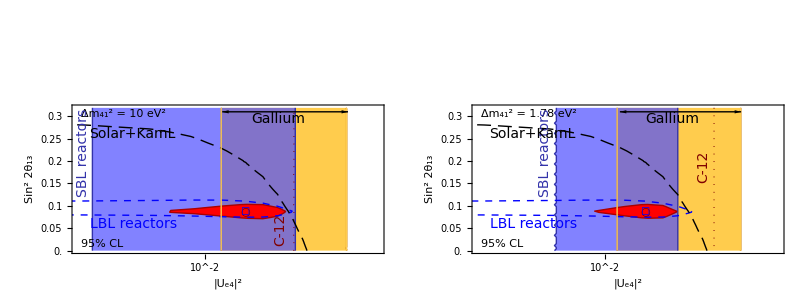

```mathematica
For[j=21,j≤22,j++,
MyCombinedPlot[j]=JHEPPlot[Show[Sequence@@Table[cleanContourPlot[MyPlot[i,j]],{i,1,Length[DataFiles]}],PlotRange->{{-3.1,-0.5},All}]];
];
Grid[{{
Show[MyCombinedPlot[21],
Epilog->{
Black,Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
Text["Δm_41^2 = "<>ToString[Round[10^dmsqTable⟦1⟧]]<>" eV^2",Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]],
Black,Text[Style["Gallium",FontSize->14],{-1.6,0.295},{-1,0}],
Arrowheads[{-0.05,0.05}],Arrow[{{-1.85,0.31},{-0.76,0.31}}],
MyStyles⟦2,1⟧,Text[Style["SBL reactors",FontSize->14],{-3,0.12},{-1,-1},{0,1}],
Darker[MyStyles⟦3,1⟧],Text[Style["All ν_e disapp",FontSize->14],{-2.05,1.3},{1,0},{0,1}],
MyStyles⟦4,1⟧,Text[Style["LBL reactors",FontSize->14],{-3,0.075},{-1,1}],
MyStyles⟦5,1⟧,Text[Style["C-12",FontSize->14],{-1.35,0.01},{-1,0},{0,1}],
MyStyles⟦6,1⟧,Text[Style["Solar+KamL",FontSize->14],{-3,0.26},{-1,0},{1,-0.1}],
Darker[MyStyles⟦3,1⟧],Text[Style["○"],BFPoint[3]⟦{1,3}⟧],
MyStyles⟦4,1⟧,Text[Style["◻"],BFPoint[3]⟦{1,3}⟧]
}],
Show[MyCombinedPlot[22],
Epilog->{
Black,Text["95% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.8]],
Text["Δm_41^2 = "<>ToString[Round[10^dmsqTable⟦2⟧,0.01]]<>" eV^2",Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]],
Black,Text[Style["Gallium",FontSize->14],{-1.65,0.295},{-1,0}],
Arrowheads[{-0.05,0.05}],Arrow[{{-1.87,0.31},{-0.82,0.31}}],
MyStyles⟦2,1⟧,Text[Style["SBL reactors",FontSize->14],{-2.52,0.12},{-1,0},{0,1}],
Darker[MyStyles⟦3,1⟧],Text[Style["All ν_e disapp",FontSize->14],{-2.05,1.3},{1,0},{0,1}],
MyStyles⟦4,1⟧,Text[Style["LBL reactors",FontSize->14],{-3,0.075},{-1,1}],
MyStyles⟦5,1⟧,Text[Style["C-12",FontSize->14],{-1.15,0.15},{-1,0},{0,1}],
MyStyles⟦6,1⟧,Text[Style["Solar+KamL",FontSize->14],{-3,0.26},{-1,0},{1,-0.1}],
Darker[MyStyles⟦3,1⟧],Text[Style["○"],BFPoint[3]⟦{1,3}⟧],
MyStyles⟦4,1⟧,Text[Style["◻"],BFPoint[3]⟦{1,3}⟧]
}
]}}]
```

### ν_μ disappearance analysis - θ_23 vs. θ_24 vs. Δm_41^2

```mathematica
(* Note: solar neutrinos are not competitive here and are therefore omitted *)
DataFiles="3-3p1/dm41th23th24-"<>#<>".dat.gz"&/@{"cdhs","atm","minos","mb200dis","evid","noevid","solar"};
(*DataFiles="3-3p1/dm41th23th24-"<>#<>".dat.gz"&/@{"minos","minos-nophases"};*)
For[i=1,i≤Length[DataFiles],i++,
Print["Reading "<>DataFiles⟦i⟧<>" ..."];
Data[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Log10[Max[1*^-4,Sin[#⟦3⟧]^2]],#⟦1⟧,Sin[#⟦2⟧]^2,Min[#⟦{-2,-1}⟧]}&/@Data[i];
Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i,2]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i,3]={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i,1]=Interpolation[Data[i,1],InterpolationOrder->1];
DataInterpol[i,2]=Interpolation[Data[i,2],InterpolationOrder->1];
DataInterpol[i,3]=Interpolation[Data[i,3],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];
p3Min[i]=Min[Data[i]⟦All,3⟧];
p3Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
Off[FindMinimum::reged,FindMinimum::lstol];
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2,p3],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]},{p3,BFPoint[i]⟦3⟧,p3Min[i],p3Max[i]}]/.Rule[s_,x_]:>x;
On[FindMinimum::reged,FindMinimum::lstol];
Print["Best fit: sin^2θ_24=",10^BFPoint[i]⟦1⟧,", Δm^2=",10^BFPoint[i]⟦2⟧,", sin^2θ_23=",BFPoint[i]⟦3⟧];
Chi2NoOsc[i]=DataInterpol[i][p1Min[i],p2Min[i],p3Min[i]];
Print["χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
];
```

Reading 3-3p1/dm41th23th24-cdhs.dat.gz ...

Best fit: sin^2θ_24=0.0711739, Δm^2=25.1189, sin^2θ_23=0.0873322

χ_min^2=9.66327, χ_(no osc)^2=14.7377, Δχ_(no osc.)^2=5.07443 (CL 0.920914)

Reading 3-3p1/dm41th23th24-atm.dat.gz ...

Best fit: sin^2θ_24=0.0001, Δm^2=0.0398107, sin^2θ_23=0.464631

χ_min^2=80.1462, χ_(no osc)^2=238.71, Δχ_(no osc.)^2=158.564 (CL 1.)

Reading 3-3p1/dm41th23th24-minos.dat.gz ...

Best fit: sin^2θ_24=0.0565302, Δm^2=17.7828, sin^2θ_23=0.5146

χ_min^2=38.8451, χ_(no osc)^2=110.588, Δχ_(no osc.)^2=71.7426 (CL 1.)

Reading 3-3p1/dm41th23th24-mb200dis.dat.gz ...

Best fit: sin^2θ_24=0.01435, Δm^2=17.7828, sin^2θ_23=0.900572

χ_min^2=63.6612, χ_(no osc)^2=65.0924, Δχ_(no osc.)^2=1.43113 (CL 0.511085)

Reading 3-3p1/dm41th23th24-evid.dat.gz ...

Best fit: sin^2θ_24=0.0223539, Δm^2=5.01187, sin^2θ_23=0.900572

χ_min^2=159.071, χ_(no osc)^2=223.716, Δχ_(no osc.)^2=64.6447 (CL 1.)

Reading 3-3p1/dm41th23th24-noevid.dat.gz ...

Best fit: sin^2θ_24=0.01435, Δm^2=17.7828, sin^2θ_23=0.464631

χ_min^2=199.061, χ_(no osc)^2=429.215, Δχ_(no osc.)^2=230.154 (CL 1.)

Reading 3-3p1/dm41th23th24-solar.dat.gz ...

Best fit: sin^2θ_24=0.0001, Δm^2=0.0398107, sin^2θ_23=0.900572

χ_min^2=254.311, χ_(no osc)^2=254.311, Δχ_(no osc.)^2=1.×10^-7 (CL 5.×10^-8)

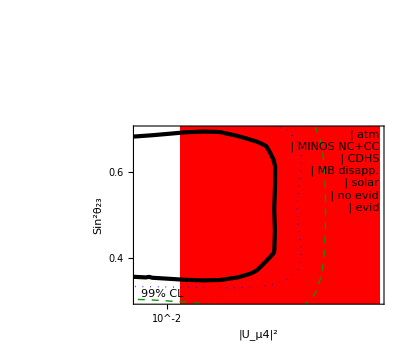
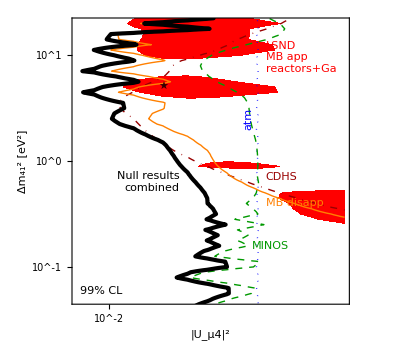
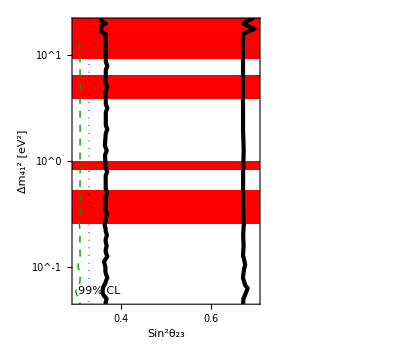
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Clear[MyPlot,MyCombinedPlot];
MyStyles={
{Directive[Thick,RGBColor[.6,0,0],DotDashed],None},
{Directive[Thick,Blue,Dotted],None},
{Directive[Thick,RGBColor[0,.6,0],Dashed],None},
{Directive[Thick,RGBColor[1,.5,0]],None},
{None,{Red,None}},
{Directive[AbsoluteThickness[3],Black],None},
{Directive[Thick,RGBColor[.6,0,.6]],None}
};
MyLegend=Framed[Grid[{
{LegendLine[MyStyles⟦2,1⟧],"atm"},
{LegendLine[MyStyles⟦3,1⟧],"MINOS NC+CC"},
{LegendLine[MyStyles⟦1,1⟧],"CDHS"},
{LegendLine[MyStyles⟦4,1⟧],"MB disapp."},
{LegendLine[MyStyles⟦7,1⟧],"solar"},
{LegendLine[MyStyles⟦6,1⟧],"no evid"},
{LegendBox[MyStyles⟦5,2,1⟧],"evid"}
},Alignment->Left,BaseStyle->{FontSize->12},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]];
(*MyLegend=Framed[Grid[{
{LegendLine[MyStyles⟦1,1⟧],"two phases marginalized"},
{LegendLine[MyStyles⟦2,1⟧],"all phases fixed at 0"}},
Alignment->Left,BaseStyle->{FontSize->12},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]]*)
For[i=1,i≤Length[DataFiles],i++,
MyOptions={PlotRange->Full,Contours->{χ2[2,0.01]},ContourShading->MyStyles⟦i,2⟧,ContourStyle->MyStyles⟦i,1⟧,ImagePadding->{{100,10},{70,10}}};
MyPlot[i,1]=ContourPlot[DataInterpol[i,1][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{LogTicks[-4,1],LogTicks[-4,4],LogTicksNoLabel[-4,1],LogTicksNoLabel[-4,4]},
Epilog->{Text["★",BFPoint[i]⟦{1,2}⟧],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.7]],
Inset[MyLegend,Scaled[{0.98,0.98}],{1,1}]}];
MyPlot[i,2]=ContourPlot[DataInterpol[i,2][p1,p3]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p3,p3Min[i],p3Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"|U_μ4|^2","Sin^2θ_23"},FrameTicks->{LogTicks[-4,1],Automatic,LogTicksNoLabel[-4,1],Automatic},
Epilog->{Text["★",BFPoint[i]⟦{1,3}⟧],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.7]],
Inset[MyLegend,Scaled[{0.98,0.98}],{1,1}]}];
MyPlot[i,3]=ContourPlot[DataInterpol[i,3][p2,p3]-Chi2Min[i],{p3,p3Min[i],p3Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2θ_23","Δm_41^2 [eV^2]"},FrameTicks->{Automatic,LogTicks[-4,4],Automatic,LogTicksNoLabel[-4,4]},
Epilog->{Text["★",BFPoint[i]⟦{3,2}⟧],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.7]]}];
];
For[j=1,j≤3,j++,
(*MyCombinedPlot[j]=JHEPPlot[Show[Sequence@@Table[MyPlot[i,j],{i,Length[DataFiles],1,-1}]]];*)
MyCombinedPlot[j]=JHEPPlot[Show[MyPlot[5,j],MyPlot[1,j],MyPlot[2,j],MyPlot[3,j],MyPlot[4,j],MyPlot[6,j]]];
];
Grid[{{Show[MyCombinedPlot[2],PlotRange->{{-2.2,-0.5},{0.3,0.7}}]},
{Show[MyCombinedPlot[1],PlotRange->{{-2.2,-0.5},{-1.3,1.3}},Epilog->{
Style[{
MyStyles⟦1,1⟧,Text["CDHS",{-1.0,-0.15},{-1,0},{1,-0.2}],
MyStyles⟦2,1⟧,Text["atm",{-1.11,0.5},{1,0},{0,1},Background->GrayLevel[1,0.7]],
MyStyles⟦3,1⟧,Text[Style["MINOS",LineSpacing->{1,0}],{-1.09,-0.8},{-1,0},Background->GrayLevel[1,0.7]],
MyStyles⟦4,1⟧,Text["MB disapp",{-1.0,-0.4},{-1,0},{1,-0.3}],
MyStyles⟦5,2,1⟧,Text[Style["LSND\nMB app\nreactors+Ga",LineSpacing->{1,0}],{-1,0.98},{-1,0}],
MyStyles⟦6,1⟧,Text[Style["Null results\ncombined",LineSpacing->{1,0}],{-1.55,-0.2},{1,0}],
RGBColor[.2,0,0],Text["★",BFPoint[5]⟦{1,2}⟧],
Black,Thickness[Medium],Dashing[{}],RGBColor[.2,0,0](*,Arrow[{{-1,0.62},{-1.5,0.7}}]*)
},FontSize->14],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,0.7]]
}],
Show[MyCombinedPlot[3],PlotRange->{{0.3,0.7},{-1.3,1.3}}]}}]
```

### ν_μ disappearance analysis in the μ-τ sector - θ_24 vs. θ_34 vs. Δm_41^2

NOTE: Data[i] has the format (sin^2 θ_24, sin^2 θ_34, Δm^2), not (U_μ4^2, U_τ4^2, Δm^2) because the scan grid would no longer be rectangular in this case.
In the definition of DataInterpol, this is corrected for, but NOT in the definitions of DataInterpol12/13/32!!!

```mathematica
DataFiles="3-3p1/th24th34dm41-"<>#<>".dat.gz"&/@{"noevid","minos","atm","mb-cdhs-reactors","solar","noevid","minos","atm","mb-cdhs-reactors","solar",
"minos-12eV2","minos-12eV2","minos-1eV2","minos-1eV2","minos-0.4eV2","minos-0.4eV2","minos-0.1eV2","minos-0.1eV2"};
DataFiles="3-3p1/th24th34dm41-"<>#<>"-phases.dat.gz"&/@{"noevid","minos"};
For[i=1,i≤Length[DataFiles],i++,
Print["Reading ",DataFiles⟦i⟧,"..."];
DataRaw[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Sin[#⟦1⟧]^2,Sin[#⟦2⟧]^2,#⟦3⟧,Min[#⟦{-2,-1}⟧]}&/@DataRaw[i];
Data[i]=Sort[#]⟦1⟧&/@Split[Data[i],#1⟦1;;3⟧==#2⟦1;;3⟧&];
Off[Interpolation::inhr];
DataInterpol[i]=Evaluate[Interpolation[Data[i],InterpolationOrder->1][#1,#2/(1-#1),#3]]&;
Data12[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Split[Sort[#⟦{1,2,3,-1}⟧&/@Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
DataInterpol12[i]=Interpolation[Data12[i],InterpolationOrder->1];
Data13[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Split[Sort[#⟦{1,3,2,-1}⟧&/@Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
DataInterpol13[i]=Interpolation[Data13[i],InterpolationOrder->1];
Data32[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Split[Sort[#⟦{3,2,1,-1}⟧&/@Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
DataInterpol32[i]=Interpolation[Data32[i],InterpolationOrder->1];
On[Interpolation::inhr];

Um4sqMin[i]=Min[Data[i]⟦All,1⟧];
Um4sqMax[i]=Max[Data[i]⟦All,1⟧];
Ut4sqMin[i]=Min[Data[i]⟦All,2⟧];
Ut4sqMax[i]=Max[Data[i]⟦All,2⟧];
If[Ut4sqMin[i]==Ut4sqMax[i],
Ut4sqMin[i]=Ut4sqMin[i-1];
Ut4sqMax[i]=Ut4sqMax[i-1];
];
dm41Min[i]=Min[Data[i]⟦All,3⟧];
dm41Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
(*{Chi2Min[i],BFPoint[i]}={BFPoint[i]⟦-1⟧,BFPoint[i]⟦1;;3⟧};*)
Off[FindMinimum::reged,FindMinimum::lstol];
If[StringCases[DataFiles⟦i⟧,"solar"]≠{},
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol12[i][Um4sq,Ut4sq],{Um4sq,BFPoint[i]⟦1⟧,Um4sqMin[i],Um4sqMax[i]},{Ut4sq,BFPoint[i]⟦2⟧,Ut4sqMin[i],Ut4sqMax[i]}]/.Rule[s_,x_]:>x;
AppendTo[BFPoint[i],0];
Chi2NoOsc[i]=DataInterpol12[i][Um4sqMin[i],Ut4sqMin[i]],
(* Else *)
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][Um4sq,Ut4sq,dm41],{Um4sq,BFPoint[i]⟦1⟧,Um4sqMin[i],Um4sqMax[i]},{Ut4sq,BFPoint[i]⟦2⟧,Ut4sqMin[i],Ut4sqMax[i]},{dm41,BFPoint[i]⟦3⟧,dm41Min[i],dm41Max[i]}]/.Rule[s_,x_]:>x;
Chi2NoOsc[i]=DataInterpol[i][Um4sqMin[i],Ut4sqMin[i],dm41Min[i]];
];
On[FindMinimum::reged,FindMinimum::lstol];
Print["Best fit: sin^2θ_24=",BFPoint[i]⟦1⟧,", sin^22θ_34=",BFPoint[i]⟦2⟧,", Δm_41^2=",10^BFPoint[i]⟦3⟧];
Print["χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];

Um4sqMin[i]=Ut4sqMin[i]=0;
(*Um4sqMax[i]=0.15;*)
(*Um4sqMin[i]=Ut4sqMin[i]=-3;*)
dm41Min[i]=-1.5;
dm41Max[i]=1.5;
];
```

Reading 3-3p1/th24th34dm41-noevid-phases.dat.gz...

Best fit: sin^2θ_24=0., sin^22θ_34=0.00562829, Δm_41^2=0.0630957

χ_min^2=202.216, χ_(no osc)^2=202.448, Δχ_(no osc.)^2=0.232367 (CL 0.109688)

Reading 3-3p1/th24th34dm41-minos-phases.dat.gz...

Best fit: sin^2θ_24=0., sin^22θ_34=0.0498102, Δm_41^2=19.9526

χ_min^2=39.6054, χ_(no osc)^2=42.5118, Δχ_(no osc.)^2=2.9065 (CL 0.76619)

```mathematica
MyContours={χ2[2,PValue[1]],χ2[2,0.1]};
MyContours={χ2[2,0.1],χ2[2,0.01]};
MyOptions={
{ContourShading->{Blue,Lighter[Blue,.5],None},ContourStyle->{Black}},
{ContourShading->{RGBColor[.3,.7,.3],Lighter[RGBColor[.3,.7,.3]],None},ContourStyle->{RGBColor[0,0.5,0]}},
{ContourShading->{RGBColor[1,.8,.3],RGBColor[1,.8,.6],None},ContourStyle->{Orange}},
{ContourShading->{RGBColor[1,.3,.3],RGBColor[1,.7,.7],None},ContourStyle->{RGBColor[.6,0,0]}},
{ContourShading->{RGBColor[1,.3,1],RGBColor[1,.7,1],None},ContourStyle->{RGBColor[.6,0,.6]}},
{ContourShading->None,ContourStyle->{Black}},
{ContourShading->None,ContourStyle->{RGBColor[0,.6,0]}},
{ContourShading->None,ContourStyle->{Orange}},
{ContourShading->None,ContourStyle->{RGBColor[.6,0,0]}},
{ContourShading->None,ContourStyle->{RGBColor[.6,0,.6]}},

{ContourShading->{RGBColor[.3,.7,.3],Lighter[RGBColor[.3,.7,.3]],None},ContourStyle->{RGBColor[0,0.5,0]}},
{ContourShading->None,ContourStyle->{RGBColor[0,.6,0]}},
{ContourShading->{RGBColor[.3,.7,.3],Lighter[RGBColor[.3,.7,.3]],None},ContourStyle->{RGBColor[0,0.5,0]}},
{ContourShading->None,ContourStyle->{RGBColor[0,.6,0]}},
{ContourShading->{RGBColor[.3,.7,.3],Lighter[RGBColor[.3,.7,.3]],None},ContourStyle->{RGBColor[0,0.5,0]}},
{ContourShading->None,ContourStyle->{RGBColor[0,.6,0]}},
{ContourShading->{RGBColor[.3,.7,.3],Lighter[RGBColor[.3,.7,.3]],None},ContourStyle->{RGBColor[0,0.5,0]}},
{ContourShading->None,ContourStyle->{RGBColor[0,.6,0]}}
}/.{(ContourStyle->x_):>(ContourStyle->(Directive[Thick,x⟦1⟧,#]&/@{Dashed,Dashing[{}]}))};
```

#### Marginalization over Δm_41^2

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot12[i]=cleanContourPlot[ContourPlot[DataInterpol12[i][Um4sq,Ut4sq]-Chi2Min[i],{Um4sq,Um4sqMin[i],Um4sqMax[i]},{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]]];
MyPlot13[i]=cleanContourPlot[ContourPlot[DataInterpol13[i][Um4sq,dm41]-Chi2Min[i],{Um4sq,Um4sqMin[i],Um4sqMax[i]},{dm41,dm41Min[i],dm41Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]]];
MyPlot32[i]=cleanContourPlot[ContourPlot[DataInterpol32[i][dm41,Ut4sq]-Chi2Min[i],{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},{dm41,dm41Min[i],dm41Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]]];
];
```

InterpolatingFunction::dmval: Input value {0.0000107143, -1.49979} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.49979, 0.0000710712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000107143, -1.49979} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

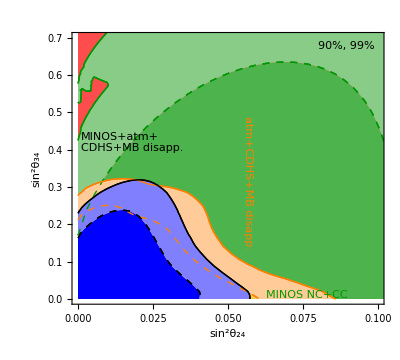

```mathematica
i=99;
MyPlot12[i]=Show[MyPlot12[4],MyPlot12[2],MyPlot12[3],MyPlot12[1],MyPlot12[8],MyPlot12[6],MyPlot12[7],MyPlot12[5],FrameLabel->{"sin^2θ_24","sin^2θ_34"},FrameTicks->Automatic,Epilog->{}];
(*MyPlot13[i]=JHEPPlot[Show[(*MyPlot13[2],*)MyPlot13[1],MyPlot13[3],MyPlot13[4],MyPlot13[5],MyPlot13[6],FrameLabel->{"sin^2θ_24","Δm_41^2 [eV^2]"},FrameTicks->{LogTicks[-5,5],LogTicks[-3,3],LogTicksNoLabel[-5,5],LogTicksNoLabel[-3,3]},Epilog->{
Text[Style["★",FontSize->24],BFPoint[1]⟦{1,3}⟧],
Text[Style["99%"],Scaled[{0.03,0.97}],{-1,1}],
Text[Style["atm + CDHS\n+ MINOS + MB",LineSpacing->{1,0}],{-1.4,-0.3},{1,0}],
Blue,Text[Style["MINOS",LineSpacing->{1,0}],{-1.5,0.8},{-1,0}],
RGBColor[0.5,0.5,0],Text[Style["MB disapp",LineSpacing->{1,0}],{-1.6,0.4},{-1,0}],
RGBColor[0.5,0,0],Text[Style["atm",LineSpacing->{1,0}],{-1.1,-1},{-1,0}],
RGBColor[0,0.5,0],Text[Style["CDHS",LineSpacing->{1,0}],{-0.9,-0.2},{-1,0}],
(*Red,Text[Style["LSND + MB app\n+ reactors + Ga",LineSpacing->{1,0}],{-1.1,0.4},{0,0}]*)(*Text[Style["Black curves: atm + CDHS + MINOS\nColors: LSND+MB app+reactors+Ga",TextAlignment->Left,FontSize->14,Background->GrayLevel[1,0.7]],Scaled[{0.03,0.03}],{-1,-1}]*)
}]];
MyPlot32[i]=JHEPPlot[Show[MyPlot32[1],MyPlot32[2],MyPlot32[4],MyPlot32[5],FrameLabel->{"sin^2θ_34","Δm_41^2 [eV^2]"},FrameTicks->{Automatic,LogTicks[-3,3],Automatic,LogTicksNoLabel[-3,3]},Epilog->{}]];*)
Grid[{(*{MyPlot13[i],Null},*)
{Show[MyPlot12[i],PlotRange->{{0,0.1},{0,0.7}},
Epilog->{Style[{
(*MyStyles⟦1,2⟧,Text[Style["ν_μ disapp\ncombined",LineSpacing->{1,0}],{0.02,0.15},{-1,0},{1,-4}],*)
RGBColor[0,.6,0],Text["MINOS NC+CC",{0.09,0.01},{1,0},{0.1,-1}],
Orange,Text["atm+CDHS+MB disapp.",{0.055,0.49},{-1,-1},{0,-1},Background->GrayLevel[1,.7]],
Black,Text[Style["MINOS+atm+\nCDHS+MB disapp.",TextAlignment->Left,LineSpacing->{1,0}],{0.001,0.39},{-1,-1}]
},FontSize->16],Text[Style["90%, 99%"],Scaled[{0.97,0.97}],{1,1}]}](*,
Show[MyPlot32[i],
Epilog->{Style[{
RGBColor[0,.6,0],Text["MINOS NC+CC",{0.55,1},{-1,1}],
Black,Text[Style["MINOS+atm+\nCDHS+MB disapp.",TextAlignment->Left,LineSpacing->{1,0}],{0.45,0.},{-1,0}]
},FontSize->16],Text[Style["68%, 90%"],Scaled[{0.97,0.97}],{1,1}]}
]*)}}]
If[SaveFigures,
Export["fig/Um4sqUt4sqdm41.pdf",MyPlot13[i]];
];
```

#### Fixed Δm_41^2

```mathematica
(* Fixed Subscript[Δm, 41]^2 plots *)
dmsqTable={Log10[12.],Log10[1.],Log10[0.4],Log10[0.1]};
For[i=1,i≤Length[DataFiles],i++,
For[k=1,k≤Length[dmsqTable],k++,
Chi2MinLocal[i,k]=NMinimize[{DataInterpol[i][Um4sq,Ut4sq,dmsqTable⟦k⟧],Um4sqMin[i]≤Um4sq≤Um4sqMax[i]&&Ut4sqMin[i]≤Ut4sq≤Ut4sqMax[i]},{Um4sq,Ut4sq}]⟦1⟧;
MyPlot12[i,k]=cleanContourPlot[ContourPlot[DataInterpol[i][10^logUm4sq,Ut4sq,dmsqTable⟦k⟧]-Chi2MinLocal[i,k],{logUm4sq,-2,Log10[Um4sqMax[i]]},{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧],ContourShading->None]];
(*MyPlot12[i,k]=cleanContourPlot[ContourPlot[DataInterpol[i][Um4sq,Ut4sq,dmsqTable⟦k⟧]-Chi2MinLocal[i,k],{Um4sq,Um4sqMin[i],Um4sqMax[i]},{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧],ContourShading->None]];*)
]; (* For[k] *)
];
```

InterpolatingFunction::dmval: Input value {0.0049002, 0.999302, 0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.914025, 9.62596, 1.07918} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.853713, 3.77902, 1.07918} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

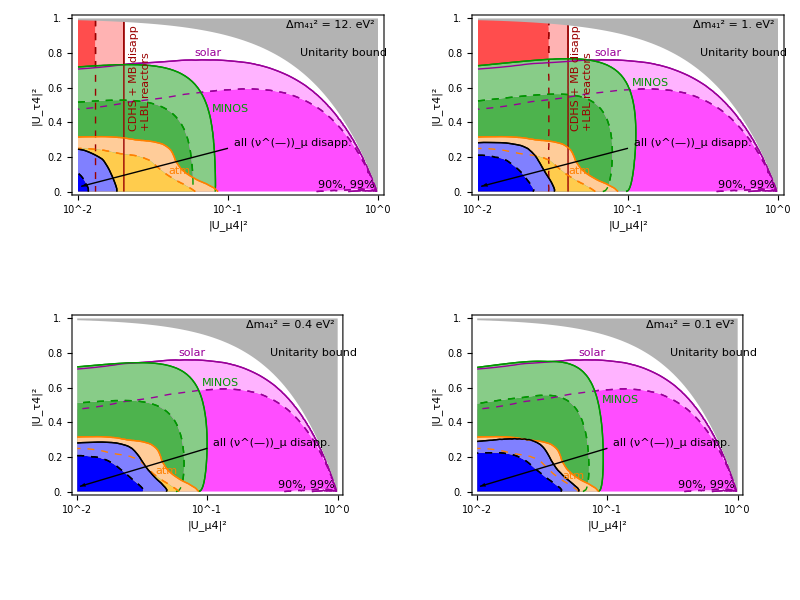

```mathematica
i=99;
UnitarityPlot=cleanContourPlot[RegionPlot[10^logUm4sq+Ut4sq>1,{logUm4sq,-2,0},{Ut4sq,0,1},PlotStyle->GrayLevel[.7]]];
For[k=1,k≤Length[dmsqTable],k++,
MyPlot12[i,k]=JHEPPlot[Show[If[k<3,MyPlot12[4,k],{}],MyPlot12[5,k],MyPlot12[10+2k-1,k],MyPlot12[3,k],MyPlot12[1,k],If[k<3,MyPlot12[9,k],{}],MyPlot12[10,k],MyPlot12[10+2k,k],MyPlot12[8,k],MyPlot12[6,k],UnitarityPlot,
PlotRange->{(*{0,0.13}*){-2,0},{0,1.0}},FrameLabel->{"|U_μ4|^2","|U_τ4|^2"},FrameTicks->{LogTicks[-3,1],Automatic,LogTicksNoLabel[-3,1],Automatic},
Epilog->{
(*GrayLevel[.7],Polygon[{{0,1},{1,1},{1,0}}],*)
Black,Text["Unitarity bound",{Log10[0.3],0.8},{-1,0},{1,-1.7}],
Text[Style["90%, 99%"],Scaled[{0.97,0.03}],{1,-1}],
Style[{Orange,Text[Style["atm",TextAlignment->Left,LineSpacing->{1,0}],
Switch[k,4,{Log10[0.045],0.06},_,{Log10[0.04],0.09}],{-1,-1},{1,-.9}],
RGBColor[0,.6,0],Text[Style["MINOS"],
Switch[k,1,{Log10[0.078],.45},2,{Log10[0.106],0.6},3,{Log10[0.09],0.6},_,{Log10[0.09],0.5}],{-1,-1}],
RGBColor[.6,0,0],Text[Style["CDHS + MB disapp\n\!\(\*StyleBox[\"+LBL reactors\",FontSize->13]\)",TextAlignment->Left,LineSpacing->{1,0},Background->GrayLevel[1,.7]],
Switch[k,1,{Log10[0.022],0.35},2,{Log10[0.042],0.35},_,{Log10[2.],0.}],{-1,1},{0,1}],
RGBColor[.6,0,.6],Text[Style["solar"],{Log10[0.06],0.77},{-1,-1}],
Black,Text[Style["all (ν^(—))_μ disapp.",TextAlignment->Left,LineSpacing->{1,0}(*,Background->GrayLevel[1,.7]*)],
Switch[k,_,{Log10[0.11],0.25}],{-0.9,-0.9}],
Arrow[{{Log10[0.1],0.25},{Log10[0.0105],0.03}}]
},FontSize->16],
Inset[Framed["Δm_41^2 = "<>ToString[Round[10^dmsqTable⟦k⟧,0.01]]<>" eV^2",Background->GrayLevel[1,.7]],Scaled[{0.97,0.97}],{1,1}]
}
]];
];
Grid[{{Show[MyPlot12[i,1]],
Show[MyPlot12[i,2]]},
{Show[MyPlot12[i,3]],
Show[MyPlot12[i,4]]}}]
```

#### Marginalization over θ_24

Load “-phases.dat.gz” files, then execute the following

```mathematica
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,(#⟦2⟧)^2,#⟦3⟧,#⟦4⟧,#⟦5⟧,Min[#⟦{-2,-1}⟧]}&/@DataRaw[i];
Data[i]=Split[Data[i],#1⟦1;;3⟧==#2⟦1;;3⟧&];
Data[i]=Sort[Union[#,#/.{p1_,p2_,p3_,0,p5_,χ_}:>{p1,p2,p3,2.π,p5,χ},#/.{p1_,p2_,p3_,p4_,0,χ_}:>{p1,p2,p3,p4,2.π,χ},#/.{p1_,p2_,p3_,0,0,χ_}:>{p1,p2,p3,2.π,2.π,χ}]]&/@Data[i];

(* Determine best and worst phases on grid *)
DeltaInterpol0[i]=Interpolation[#⟦All,-3;;-1⟧,InterpolationOrder->{0,3}]&/@Data[i];
DeltaInterpol[i]=Function[{δ1,δ2},#[Mod[δ1,2π],Mod[δ2,2π]]]&/@DeltaInterpol0[i];
RoughBF[i]=Sort[#,OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧&/@Data[i];
RoughWF[i]=Sort[#,OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦-1⟧&/@Data[i];

(* Refine best and worst phases *)
DeltaMinima[i]={};
DeltaMaxima[i]={};
Off[InterpolatingFunction::dmval,InterpolatingFunction::dprec,FindMinimum::lstol,FindMaximum::lstol,FindMinimum::nrnum,FindMaximum::nrnum,FindMinimum::fmgz,FindMaximum::fmgz,FindMinimum::reged,FindMaximum::reged];
For[k=1,k≤Length[DeltaInterpol[i]],k++,
(*AppendTo[DeltaMinima[i],{DeltaInterpol[i]⟦k⟧[0,π/2.]}];
AppendTo[DeltaMaxima[i],{DeltaInterpol[i]⟦k⟧[0,2.π]}];*)
AppendTo[DeltaMinima[i],FindMinimum[DeltaInterpol[i]⟦k⟧[0,δ2],{δ2,RoughBF[i]⟦k,5⟧,0,2.1π}]];
AppendTo[DeltaMaxima[i],FindMaximum[DeltaInterpol[i]⟦k⟧[0,δ2],{δ2,RoughWF[i]⟦k,5⟧,0,2.1π}]];
];
On[InterpolatingFunction::dmval,InterpolatingFunction::dprec,FindMinimum::lstol,FindMaximum::lstol,FindMinimum::nrnum,FindMaximum::nrnum];

(* Interpolate data for best and worst phases *)
DataMin[i]=Table[{Data[i]⟦j,1,1⟧,Data[i]⟦j,1,2⟧,Data[i]⟦j,1,3⟧,DeltaMinima[i]⟦j,1⟧},{j,1,Length[Data[i]]}];
DataMax[i]=Table[{Data[i]⟦j,1,1⟧,Data[i]⟦j,1,2⟧,Data[i]⟦j,1,3⟧,DeltaMaxima[i]⟦j,1⟧},{j,1,Length[Data[i]]}];
Data32Min[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Split[Sort[#⟦{3,2,1,-1}⟧&/@DataMin[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data32Max[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Split[Sort[#⟦{3,2,1,-1}⟧&/@DataMax[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
DataInterpol32Min[i]=Interpolation[Data32Min[i],InterpolationOrder->1];
DataInterpol32Max[i]=Interpolation[Data32Max[i],InterpolationOrder->1];
];
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaximum :: sdprec will be suppressed during this calculation.

FindMaximum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

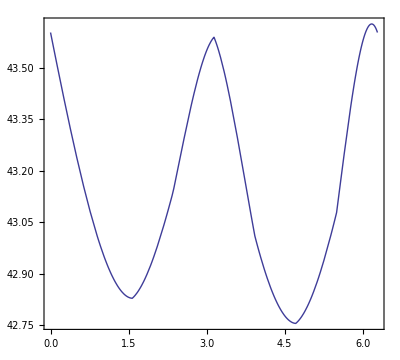

{43.6018}

```mathematica
i=2;
k=444;
Plot[DeltaInterpol[i]⟦k⟧[0,δ],{δ,0,2π}]
DeltaMaxima[i]⟦k⟧
```

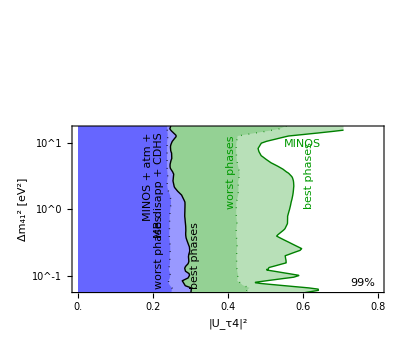

```mathematica
MyContours={χ2[2,0.01]};
MyOptions={
{ContourShading->{Blue,None},ContourStyle->{Black}},
{ContourShading->{RGBColor[.3,.7,.3],None},ContourStyle->{RGBColor[0,0.5,0]}},
{ContourShading->None,ContourStyle->{Black}},
{ContourShading->None,ContourStyle->{RGBColor[0,.6,0]}}
};
MyOptions=Join[
MyOptions/.{(ContourStyle->x_):>(ContourStyle->(Directive[Thick,x⟦1⟧])),(ContourShading->{c_,None}):>(ContourShading->{Lighter[c,.6],None})},
MyOptions/.{(ContourStyle->x_):>(ContourStyle->(Directive[Dotted,Thick,x⟦1⟧])),
(ContourShading->{c_,None}):>((ContourShading->{Lighter[c,.4],None}))}
];
For[i=1,i≤Length[DataFiles],i++,
MyPlot32Min[i]=cleanContourPlot[ContourPlot[DataInterpol32Min[i][dm41,Ut4sq]-Chi2Min[i],{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},{dm41,dm41Min[i],dm41Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]]];
MyPlot32Max[i]=cleanContourPlot[ContourPlot[DataInterpol32Max[i][dm41,Ut4sq]-Chi2Min[i],{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},{dm41,dm41Min[i],dm41Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦4+i⟧]]];
];
MyPlot32[i]=JHEPPlot[Show[MyPlot32Min[2],MyPlot32Max[2],MyPlot32Min[1],MyPlot32Max[1],PlotRange->{{0,0.8},{-1.2,1.2}},FrameLabel->{"|U_τ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{Automatic,LogTicks[-3,3],Automatic,LogTicksNoLabel[-3,3]},
Epilog->{
Text[Style["99%"],Scaled[{0.97,0.03}],{1,-1}],
RGBColor[0,.6,0],Text[Style["MINOS"],{0.55,0.9},{-1,-1}],
Black,Text[Style["MINOS + atm +\nMB disapp + CDHS",LineSpacing->{1,0}],{0.23,1.15},{1,-1},{0,1}],
(*Red,Text["WRONG!!!",{0.5,0},{0,0}],*)
Style[{RGBColor[0,.6,0],Text["best phases",{0.63,0},{-1,-1},{0,1}],Text["worst phases",{0.42,0},{-1,-1},{0,1}],
Black,Text["best phases",{0.3,-1.2},{-1,1},{0,1}],Text["worst phases",{0.23,-1.2},{-1,-1},{0,1}]},FontSize->14]
}
]]
```

```mathematica
i=2;
Data[i]={Sin[#⟦1⟧]^2,Sin[#⟦2⟧]^2,#⟦3⟧,#⟦4⟧,#⟦5⟧,Min[#⟦{-2,-1}⟧]}&/@DataRaw[i];
Data[i]=#⟦3⟧&/@Split[Data[i],#1⟦1;;3⟧==#2⟦1;;3⟧&];
Data[i]={#⟦2⟧,#⟦3⟧,#⟦-1⟧}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
```

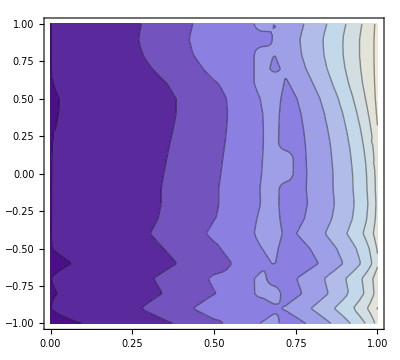

```mathematica
ContourPlot[DataInterpol[i][s2th34,logDmsq],{s2th34,0,1},{logDmsq,-1,1}]
```

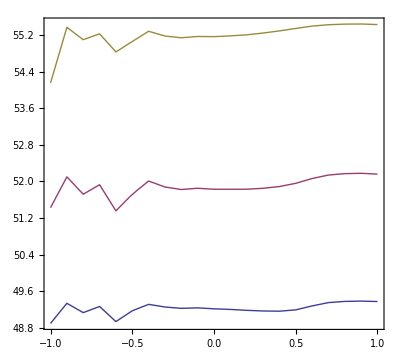

```mathematica
Plot[{DataInterpol[i][0.6,logDmsq],DataInterpol[i][0.7,logDmsq],DataInterpol[i][0.8,logDmsq]},{logDmsq,-1,1}]
```

#### Some experiments

```mathematica
i=1;
XXX={#⟦1,1⟧,#⟦1,2⟧,Interpolation[#,InterpolationOrder->{0,0,3}]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
MyInterpol[p1_,p2_,p3_]:=Interpolation[{#⟦1⟧,#⟦2⟧,#⟦3⟧[#⟦1⟧,#⟦2⟧,Log10[p3]]}&/@XXX,InterpolationOrder->1][p1,p2]
```

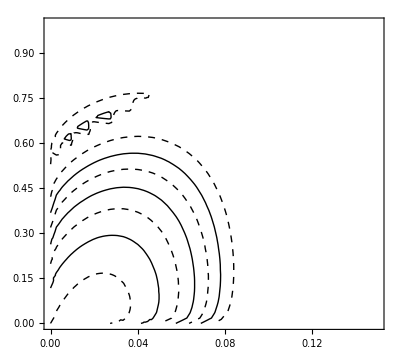

```mathematica
i=1;
cleanContourPlot[ContourPlot[MyInterpol[Um4sq,Ut4sq,0.1]-Chi2Min[i],{Um4sq,Um4sqMin[i],Um4sqMax[i]},{Ut4sq,Ut4sqMin[i],Ut4sqMax[i]},Contours->{1,2,3,4,5,6,7,8,9.2},PlotRange->Full,ContourShading->False,Evaluate[Sequence@@MyOptions⟦i⟧]]]
```

### Impact on SM parameters - θ_23 vs. θ_13 vs. Δm_31^2

```mathematica
DataFiles="2-smparams/"<>#&/@{"th23dm31-4f-all.dat.gz","th13dm31-4f-all.dat.gz","th23th13-4f-all.dat.gz",
"th23dm31-3f-all.dat.gz","th13dm31-3f-all.dat.gz","th23th13-3f-all.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,{-2,-1}⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]=Switch[Mod[i,3],
1,{Sin[#⟦1⟧]^2,#⟦2⟧,#⟦3⟧}&/@Data[i],
2,{Sin[2*10^#⟦1⟧]^2,#⟦2⟧,#⟦3⟧}&/@Data[i],
0,{Sin[#⟦1⟧]^2,Sin[2*10^#⟦2⟧]^2,#⟦3⟧}&/@Data[i]
];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]}]/.Rule[s_,x_]:>x;
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum :: lstol will be suppressed during this calculation.

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
MyOptions={{ContourShading->(Lighter[#]&/@{Gray,Blue,Red,Cyan,White}),ContourStyle->None},{ContourShading->None,ContourStyle->(Directive[Thick,Black,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})}};
MyFrameLabels={{"Sin^2 θ_23","Δm_31^2 [eV^2]"},{"Sin^2 2θ_13","Δm_31^2 [eV^2]"},{"Sin^2 θ_23","Sin^2 2θ_13"}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦Floor[(i-1)/3]+1⟧],FrameLabel->MyFrameLabels⟦Mod[i-1,3]+1⟧,ImagePadding->{{100,20},{50,20}}];
];
```

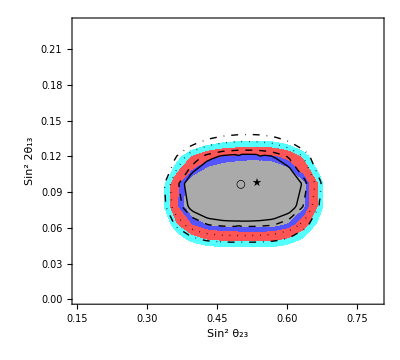
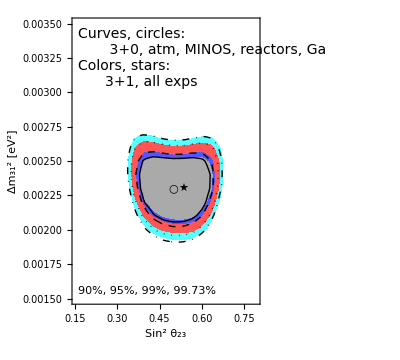
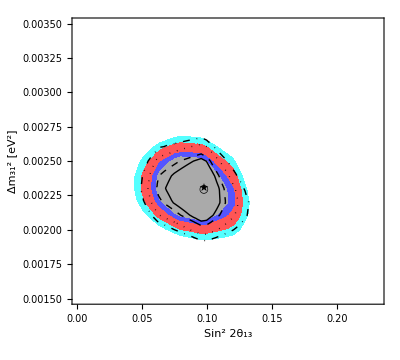
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Grid[{{
Show[MyPlot[3],MyPlot[6],PlotRange->All,Epilog->{Text["★",BFPoint[3]],Text["○",BFPoint[6]]}],Null},
{Show[MyPlot[1],MyPlot[4],PlotRange->All,Epilog->{
Text["★",BFPoint[1]],Text["○",BFPoint[4]],
Text["90%, 95%, 99%, 99.73%",Scaled[{0.03,0.03}],{-1,-1}],Text[Style["Curves, circles:\n       3+0, atm, MINOS, reactors, Ga\nColors, stars:\n      3+1, all exps",TextAlignment->Left,FontSize->14],Scaled[{0.03,0.97}],{-1,1}]}],
Show[MyPlot[2],MyPlot[5],PlotRange->All,Epilog->{Text["★",BFPoint[2]],Text["○",BFPoint[5]]}]}}]
Export["fig/th23dm31th13.eps",%];
If[SaveFigures,
Export["fig/th23dm31th13.eps",%];
];
```

### 3+2 fit

#### Δm_41^2 vs. Δm_51^2

```mathematica
DataFiles=Join["4-3p2/dm41dm51-"<>#<>"-3p2.dat.gz"&/@{"all","app","disapp","app","disapp"},
"5-1p3p1/dm41dm51-"<>#<>"-1p3p1.dat.gz"&/@{"all","app","disapp","app","disapp"}];
BFPFiles=Join["4-3p2/pg/"<>#<>".dat"&/@{"all","app","disapp","app","disapp"},
"5-1p3p1/pg/"<>#<>".dat"&/@{"all","app","disapp","app","disapp"}];
Clear[Data,DataRaw,DataInterpol,BFP,Chi2Min];
For[i=1,i≤Length[DataFiles],i++,
Print["Loading ",DataFiles⟦i⟧," and ",BFPFiles⟦i⟧,"..."];
DataRaw[i]=Cases[KPImport[DataFiles⟦i⟧],{Repeated[_Real|_Integer]}];
Data[i]={#⟦1⟧,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@DataRaw[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
(*BFPoint[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1,1;;2⟧;

(* Refine BFP *)
{Chi2Min[i],BFPoint[i]}=({#⟦1⟧,{p1,p2}/.#⟦2⟧}&)[FindMinimum[DataInterpol[i][p1,p2],{p1,BFPoint[i]⟦1⟧},{p2,BFPoint[i]⟦2⟧}]];
Print["χ_min^2 = ",Chi2Min[i],", best fit: ",10^BFPoint[i]];*)

(* NEW: Load BFP from separate file *)
DataBFPRaw[i]=KPImport[BFPFiles⟦i⟧];
DataBFP[i]={#⟦1⟧,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[DataBFPRaw[i],{Repeated[_Real|_Integer]}];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataBFPRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"DM51"]]};
Print["χ_min^2 = ",Chi2Min[i],", best fit: ",BFP[i]⟦{1,2}⟧],

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataBFPRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[DataBFP[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
(*BFP[i]=Select[DataBFP[i],#⟦-1⟧==Chi2Min[i]&]⟦1,{1,2}⟧;*)

(* Extract best fit parameters *)
Params[i]=Import[BFPFiles⟦i⟧,"String"];
Params[i]=StringCases[Params[i],RegularExpression["(?m)^.*chi\\^2 "<>ToString[Floor[Chi2Min[i],0.01]]<>"[^a-zA-Z]*(.*)\n"]->"$1"]⟦1⟧;
Params[i]=#⟦1⟧->#⟦2⟧&/@Partition[ImportString[Params[i],"Table"]⟦1⟧,2];
BFP[i]=Log10[Abs[{"DM41","DM51"}/.Params[i]]];
Print["χ_min^2 = ",Chi2Min[i],", best grid point: ",10.^BFP[i]];
]; (* End[if] *)
];
```

Loading 4-3p2/dm41dm51-all-3p2.dat.gz and 4-3p2/pg/all.dat...

χ_min^2 = 701.182, best grid point: {0.872518,0.469161}

Loading 4-3p2/dm41dm51-app-3p2.dat.gz and 4-3p2/pg/app.dat...

χ_min^2 = 72.686, best grid point: {1.23726,0.573875}

Loading 4-3p2/dm41dm51-disapp-3p2.dat.gz and 4-3p2/pg/disapp.dat...

χ_min^2 = 602.674, best grid point: {0.437418,0.87708}

Loading 4-3p2/dm41dm51-app-3p2.dat.gz and 4-3p2/pg/app.dat...

χ_min^2 = 72.686, best grid point: {1.23726,0.573875}

Loading 4-3p2/dm41dm51-disapp-3p2.dat.gz and 4-3p2/pg/disapp.dat...

χ_min^2 = 602.674, best grid point: {0.437418,0.87708}

Loading 5-1p3p1/dm41dm51-all-1p3p1.dat.gz and 5-1p3p1/pg/all.dat...

χ_min^2 = 694.005, best grid point: {0.874179,0.470281}

Loading 5-1p3p1/dm41dm51-app-1p3p1.dat.gz and 5-1p3p1/pg/app.dat...

χ_min^2 = 74.5507, best grid point: {1.75801,0.49615}

Loading 5-1p3p1/dm41dm51-disapp-1p3p1.dat.gz and 5-1p3p1/pg/disapp.dat...

χ_min^2 = 602.687, best grid point: {0.437049,0.877252}

Loading 5-1p3p1/dm41dm51-app-1p3p1.dat.gz and 5-1p3p1/pg/app.dat...

χ_min^2 = 74.5507, best grid point: {1.75801,0.49615}

Loading 5-1p3p1/dm41dm51-disapp-1p3p1.dat.gz and 5-1p3p1/pg/disapp.dat...

χ_min^2 = 602.687, best grid point: {0.437049,0.877252}

```mathematica
(*MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
MyShadings[_]:={Gray,Blue,Red,Cyan,None};
MyShadings[2|3]:=None;
MyContourStyles[_]:=Black;
MyContourStyles[2]:=Orange;
MyContourStyles[3]:=Blue;*)

(*Clear[MyShadings,MyContourStyles];
MyContours={χ2[2,0.1],χ2[2,0.01]};
MyShadings[_]:={Red,Lighter[Red],None};
MyShadings[2|3]:=None;
MyShadings[2]={RGBColor[.3,.3,1,.5],RGBColor[.7,.7,1,.5],None};
(*MyShadings[3]={RGBColor[.5,1,.5,.5],RGBColor[.7,1,.7,.5],None};*)
MyContourStyles[_]:=RGBColor[.6,0,0];
MyContourStyles[2]:=Directive[Blue,#]&/@{Dashing[{}],Dotted};
MyContourStyles[3]:=Directive[RGBColor[0,.6,0],Thick,#]&/@{Dashing[{}],Dotted};*)

Clear[MyShadings,MyContourStyles,MyContours];
MyContours[_]:={χ2[2,0.05]};
MyContours[1|6]:={χ2[2,0.05],χ2[2,0.01]};
MyShadings[_]:=None;
MyShadings[1|6]:={RGBColor[1,0,0,1],RGBColor[1,.5,.5,1],None};
MyShadings[2|7]={RGBColor[.5,.5,1,.5],None};
MyShadings[3|8]={RGBColor[.5,1,.5,.5],None};
MyContourStyles[_]:=Black;
MyContourStyles[2|7]:=Directive[Blue,#]&/@{Dashing[{}]};
MyContourStyles[3|8]:=Directive[RGBColor[0,.6,0],#]&/@{Dashing[{}]};
MyContourStyles[4|9]:=MyContourStyles[2]/.{Dashing[{}]->Dotted};
MyContourStyles[5|10]:=MyContourStyles[3]/.{Dashing[{}]->Dotted};

For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][logdm41,logdm51]-Chi2Min[i],{logdm41,-1,1},{logdm51,-1,1},PlotRange->Full,Contours->MyContours[i],PlotRange->All,ContourShading->MyShadings[i],ContourStyle->MyContourStyles[i],FrameTicks->{LogTicks[-5,5],LogTicks[-5,5],LogTicksNoLabel[-5,5],LogTicksNoLabel[-5,5]},FrameLabel->{"|Δm_41^2| [eV^2]","|Δm_51^2| [eV^2]"},RegionFunction->If[StringCases[DataFiles⟦i⟧,"1p3p1"]≠{},(#1>#2&),(#2≥#1&)]];
];
```

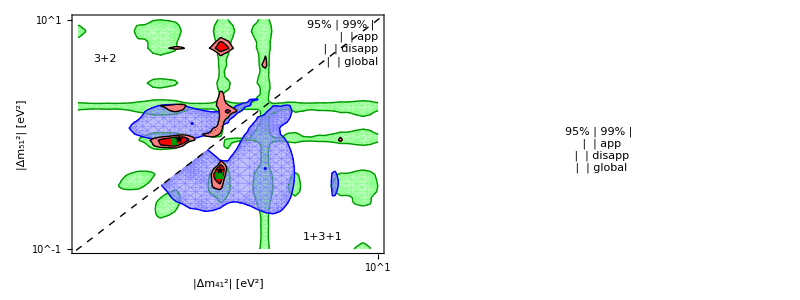

```mathematica
(*MyLegend=Framed[Grid[{
{"90%","99%",""},
{LegendLine[MyContourStyles[2]⟦1⟧],LegendLine[MyContourStyles[2]⟦2⟧],"App"},
{LegendLine[MyContourStyles[3]⟦1⟧],LegendLine[MyContourStyles[3]⟦2⟧],"Disapp"},
{LegendBox[MyShadings[1]⟦1⟧,MyContourStyles[1]],LegendBox[MyShadings[1]⟦2⟧,MyContourStyles[1]],"global"}
},Alignment->Left,BaseStyle->{FontSize->12},Spacings->{0.7,0}],Background->RGBColor[1,1,1,.7]];*)
MyLegend=Framed[Grid[{
{"95%","99%",""},
{LegendBox[MyShadings[2]⟦1⟧,MyContourStyles[2],"•",MyContourStyles[2]⟦1⟧],"","app"},
{LegendBox[MyShadings[3]⟦1⟧,MyContourStyles[3],"◼",MyContourStyles[3]⟦1⟧],"","disapp"},
{LegendBox[MyShadings[1]⟦1⟧,MyContourStyles[1],"★",MyContourStyles[1]],LegendBox[MyShadings[1]⟦2⟧,MyContourStyles[1],"★",MyShadings[1]⟦2⟧],"global"}
},Alignment->Left,BaseStyle->{FontSize->16},Spacings->{0.2,0}],Background->RGBColor[1,1,1,.7]];
MyCombiPlot=Grid[{{Show[MyPlot[3],MyPlot[2],MyPlot[1],MyPlot[5],MyPlot[4],
MyPlot[8],MyPlot[7],MyPlot[6],MyPlot[10],MyPlot[9],
Epilog->{
Dashed,Line[{{-5,-5},{5,5}}],
(*Text["90%, 95%, 99%, 99.73%",Scaled[{0.97,0.03}],{1,-1}],*)
(*Text["90%, 99%",Scaled[{0.97,0.03}],{1,-1}],*)
Text["3+2",{-0.9,0.7},{-1,1}],
Text["1+3+1",{0.5,-0.9},{-1,0}],
MyContourStyles[3]⟦1⟧,Text["◼",Sort[BFP[3]]],
MyContourStyles[2]⟦1⟧,Text["•",Sort[BFP[2]]],
MyContourStyles[1],Text["★",Sort[BFP[1]]],
MyContourStyles[8]⟦1⟧,Text["◼",Reverse[Sort[BFP[8]]]],
MyContourStyles[7]⟦1⟧,Text["•",Reverse[Sort[BFP[7]]]],
MyContourStyles[6],Text["★",Reverse[Sort[BFP[6]]]],
Inset[MyLegend/.{Rule[FontSize,16]->Rule[FontSize,14]},Scaled[{0.98,0.98}],{1,1}]
(*Text["★",Sort[BFP[2],Greater]],*)
}],
Graphics[{},Epilog->{Inset[MyLegend,Scaled[{0.5,0.5}]]}]
}}]
If[SaveFigures,
Export["fig/dm41dm51.eps",MyCombiPlot];
];
```

#### U_e4 U_μ4 vs. U_e5 U_μ5

```mathematica
DataFiles="4-3p2/Ue4Um4_Ue5Um5-dm0.9-6-"<>#<>".dat.gz"&/@{"all","app","disapp","disapp"};
DataFiles="4-3p2/Ue4Um4_Ue5Um5-dm0.5-0.9-"<>#<>".dat.gz"&/@{"all","app","disapp","disapp"};
DataFiles="5-1p3p1/Ue4Um4_Ue5Um5-dm-0.9-0.5-"<>#<>".dat.gz"&/@{"all","app","disapp","disapp"};
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=KPImport[DataFiles⟦i⟧];
ThisDM41=Cases[DataRaw[i],{"#","DM41","=",x_}:>x]⟦1⟧;
ThisDM51=Cases[DataRaw[i],{"#","DM51","=",x_}:>x]⟦1⟧;
Data[i]=Cases[DataRaw[i],{Repeated[_Real|_Integer]}];
Data[i]={#⟦1⟧,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

(* Refine BFP *)
(*Off[FindMinimum::lstol,InterpolatingFunction::dmval];
{Chi2Min[i],BFP[i]}=({#⟦1⟧,{p1,p2}/.#⟦2⟧}&)[FindMinimum[DataInterpol[i][p1,p2],{p1,BFP[i]⟦1⟧},{p2,BFP[i]⟦2⟧}]];
On[FindMinimum::lstol,InterpolatingFunction::dmval];*)

(* Extract best fit point: Either it has been computed accurate, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[Abs[ExtractParam[BFP[i],"Ue4Um4"]]],Log10[Abs[ExtractParam[BFP[i],"Ue5Um5"]]]};
Print["χ_min^2 = ",Chi2Min[i],", best fit: ",BFP[i]⟦{1,2}⟧],

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1,{1,2}⟧;
Print["χ_min^2 = ",Chi2Min[i],", best grid point: ",BFP[i]];
]; (* End[if] *)
];
```

χ_min^2 = 695.537, best fit: {-1.72951,-1.65286}

χ_min^2 = 79.3029, best fit: {-1.92602,-1.43454}

χ_min^2 = 604.52, best grid point: {-2.05,-2.5}

χ_min^2 = 604.52, best grid point: {-2.05,-2.5}

```mathematica
MyContours={χ2[2,0.1],(*χ2[2,0.05],*)χ2[2,0.01](*,χ2[2,PValue[3]]*)};
MyStyles={
{Black,Join[(Directive[Lighter[Red,#]]&/@{0,.4}),{None}](*{Gray,Blue,Red,Cyan,None}*)},
{Directive[RGBColor[0,0,0.6],#]&/@{Dashed,Dashing[{}]},Join[(Directive[Lighter[Blue,#],Opacity[0.2]]&/@{0,.4}),{None}]},
{Directive[Thick,RGBColor[0,.6,0],#]&/@{Dashed,Dashing[{}]},{RGBColor[.2,.8,.2,.5],RGBColor[.5,1,.5,.5],None}},
{Directive[Thick,RGBColor[0,.6,0],#]&/@{Dashed,Dashing[{}]},{None}}
(*{Directive[Thick,RGBColor[1,0.7,0.1],#]&/@{Dotted,DotDashed,Dashed,Dashing[{}]},None}*)
};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][Ue4Um4,Ue5Um5]-Chi2Min[i],{Ue4Um4,-3,-0.5},{Ue5Um5,-3,-0.5},PlotRange->Full,Contours->MyContours,PlotRange->All,ContourStyle->MyStyles⟦i,1⟧,ContourShading->MyStyles⟦i,2⟧,FrameTicks->{LogTicks[-5,5],LogTicks[-5,5],LogTicksNoLabel[-5,5],LogTicksNoLabel[-5,5]},FrameLabel->{"|U_e4U_μ4|","|U_e5U_μ5|"}];
];
```

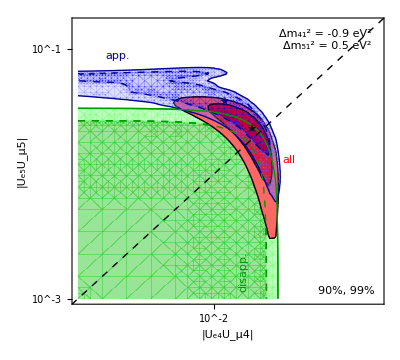

```mathematica
MyCombiPlot=Show[MyPlot[3],MyPlot[1],MyPlot[2],MyPlot[4],
PlotRange->{{-3,-0.8},{-3,-0.8}},
Epilog->{
Dashed,Line[{{-5,-5},{5,5}}],
Text[Style["Δm_41^2 = "<>ToString[ThisDM41]<>" eV^2\nΔm_51^2 = "<>ToString[ThisDM51]<>" eV^2",TextAlignment->Left,LineSpacing->{1.1,0}],(*Scaled[{0.03,0.96}],{-1,1},*)Scaled[{0.96,0.96}],{1,1},Background->GrayLevel[1,0.7]],
Text["90%, 99%"(*"90%, 95%, 99%, 99.73%"*),Scaled[{0.97,0.03}],{1,-1},Background->GrayLevel[1,0.7]],
Switch[ThisDM41,
.4|.5,{Text["★",BFP[1]],MyStyles⟦1,2,1⟧,Text["all",{-2.2,-1.75},{1,1}],
MyStyles⟦2,1,1⟧,Text["★",BFP[2]],Text["app.",{-1.8,-1.1},{-1,1}],
MyStyles⟦3,1,1⟧,(*Text["★",BFP[3]],*)Text["disapp.",{-1.6,-2.9},{-1,-1},{0,1}]},
.9,{Text["★",BFP[1]],MyStyles⟦1,2,1⟧,Text["all",{-2.1,-1.85},{1,1}],
MyStyles⟦2,1,1⟧,Text["★",BFP[2]],Text["app.",{-1.3,-2.1},{-1,-1}],
MyStyles⟦3,1,1⟧,(*Text["★",BFP[3]],*)Text["disapp.",{-1.75,-2.95},{-1,-1},{0,1}]},
-.9,{Text["★",BFP[1]],MyStyles⟦1,2,1⟧,Text["all",{-1.5,-1.85},{-1,1}],
MyStyles⟦2,1,1⟧,Text["★",BFP[2]],Text["app.",{-2.8,-1.1},{-1,-1}],
MyStyles⟦3,1,1⟧,(*Text["★",BFP[3]],*)Text["disapp.",{-1.75,-2.95},{-1,-1},{0,1}]},
_,Black
]
}]
```

#### Phases in SBL experiments for the 3+2 scenario

```mathematica
i=1;
Data[i]=Cases[KPImport["4-3p2/delta1delta2-3p2-all.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1⟧,#⟦2⟧,Min[#⟦-2⟧,#⟦-1⟧]}&/@Data[i];
```

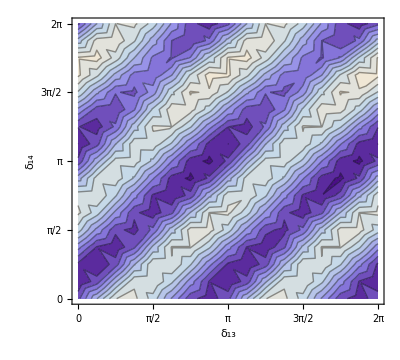

```mathematica
MyTicks={{0,"0"},{π/2,"π/2"},{π,"π"},{3π/2,"3π/2"},{2π,"2π"}};
ListContourPlot[Data[i],FrameLabel->{"δ_13","δ_14"},FrameTicks->{MyTicks,MyTicks,None,None}]
```

### More Global fits

#### θ_24 vs. θ_34

```mathematica
DataFiles="3-3p1/"<>#&/@{"th24th34-all.dat.gz","th24th34-evid.dat.gz","th24th34-noevid.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,{-2,-1}⟧]}&/@Split[Data[i],#1⟦1;;2⟧==#2⟦1;;2⟧&];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

th24Min[i]=Min[Data[i]⟦All,1⟧];
th24Max[i]=Max[Data[i]⟦All,1⟧];
th34Min[i]=Min[Data[i]⟦All,2⟧];
th34Max[i]=Max[Data[i]⟦All,2⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][th24,th34],{th24,BFPoint[i]⟦1⟧,th24Min[i],th24Max[i]},{th34,BFPoint[i]⟦2⟧,th34Min[i],th34Max[i]}]/.Rule[s_,x_]:>x;
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::reged: The point TraditionalForm`{0.0001, 0.0500929} is at the edge of the search region TraditionalForm`{0.0001, 0.45} in coordinate TraditionalForm`1 and the computed search direction points outside the region.

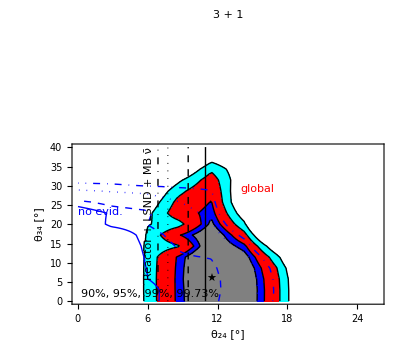

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
MyOptions={{ContourShading->{Gray,Blue,Red,Cyan,None},ContourStyle->Black},
{ContourShading->None,ContourStyle->(Directive[Thick,Black,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})},
{ContourShading->None,ContourStyle->(Directive[Thick,Blue,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][th24 Degree,th34 Degree]-Chi2Min[i],{th24,th24Min[i]/Degree,th24Max[i]/Degree},{th34,th34Min[i]/Degree,th34Max[i]/Degree},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]]
];
MyCombinedPlot[1]=Show[MyPlot[1],MyPlot[2],MyPlot[3],
FrameLabel->{"θ_24 [°]","θ_34 [°]"},PlotLabel->"3 + 1",
Epilog->{
Text["90%, 95%, 99%, 99.73%",Scaled[{0.03,0.03}],{-1,-1}],Text["★",BFPoint[1]/Degree],
Black,Text["Reactor + LSND + MB ν̄",{6.5,40},{1,-1},{0,1},Background->GrayLevel[1,0.5]],
Red,Text["global",{14,28},{-1,-1},{0.2,-1}],
Blue,Text["no evid.",{0,22},{-1,-1},{0.4,-1}]
}]
If[SaveFigures,
Export["fig/global-fit-3p2.eps",MyCombinedPlot[1]];
];
```

### Parameter goodness of fit test

```mathematica
n=3;
U3=RotationMatrix[-"TH23",{UnitVector[n,2],UnitVector[n,3]}].
DiagonalMatrix[{Exp[-I "DELTA_0"],1,1}].RotationMatrix[-"TH13",{UnitVector[n,1],UnitVector[n,3]}].DiagonalMatrix[{Exp[I "DELTA_0"],1,1}].
RotationMatrix[-"TH12",{UnitVector[n,1],UnitVector[n,2]}];

n=4;
U4=RotationMatrix[-"TH34",{UnitVector[n,3],UnitVector[n,4]}].
DiagonalMatrix[{1,1,1,Exp[-I "DELTA_1"]}].RotationMatrix[-"TH24",{UnitVector[n,2],UnitVector[n,4]}].DiagonalMatrix[{1,1,1,Exp[I "DELTA_1"]}].
RotationMatrix[-"TH14",{UnitVector[n,1],UnitVector[n,4]}].
RotationMatrix[-"TH23",{UnitVector[n,2],UnitVector[n,3]}].
DiagonalMatrix[{1,1,Exp[-I "DELTA_0"],1}].RotationMatrix[-"TH13",{UnitVector[n,1],UnitVector[n,3]}].DiagonalMatrix[{1,1,Exp[I "DELTA_0"],1}].
DiagonalMatrix[{1,Exp[-I "DELTA_2"],1,1}].RotationMatrix[-"TH12",{UnitVector[n,1],UnitVector[n,2]}].DiagonalMatrix[{1,Exp[I "DELTA_2"],1,1}];

n=5;
U5=RotationMatrix[-"TH45",{UnitVector[n,4],UnitVector[n,5]}].
RotationMatrix[-"TH35",{UnitVector[n,3],UnitVector[n,5]}].
RotationMatrix[-"TH25",{UnitVector[n,2],UnitVector[n,5]}].
DiagonalMatrix[{1,1,1,1,Exp[-I "DELTA_2"]}].RotationMatrix[-"TH15",{UnitVector[n,1],UnitVector[n,5]}].DiagonalMatrix[{1,1,1,1,Exp[I "DELTA_2"]}].
RotationMatrix[-"TH34",{UnitVector[n,3],UnitVector[n,4]}].
RotationMatrix[-"TH24",{UnitVector[n,2],UnitVector[n,4]}].
DiagonalMatrix[{1,1,1,Exp[-I "DELTA_1"],1}].RotationMatrix[-"TH14",{UnitVector[n,1],UnitVector[n,4]}].DiagonalMatrix[{1,1,1,Exp[I "DELTA_1"],1}].
RotationMatrix[-"TH23",{UnitVector[n,2],UnitVector[n,3]}].
DiagonalMatrix[{1,1,Exp[-I "DELTA_0"],1,1}].RotationMatrix[-"TH13",{UnitVector[n,1],UnitVector[n,3]}].DiagonalMatrix[{1,1,Exp[I "DELTA_0"],1,1}].
RotationMatrix[-"TH12",{UnitVector[n,1],UnitVector[n,2]}];

n=4;
DataFiles="3-3p1/pg/"<>#<>".dat"&/@{"all","disapp","app"};
DataFiles="3-3p1/pg/nombapp/"<>#<>".dat"&/@{"all","disapp","app"};
(*n=5;
DataFiles="4-3p2/pg/"<>#<>".dat"&/@{"all","disapp","app"};
DataFiles="5-1p3p1/pg/"<>#<>".dat"&/@{"all","disapp","app"};
DataFiles="4-3p2/pg/nombapp/"<>#<>".dat"&/@{"all","disapp","app"};*)
For[i=1,i≤Length[DataFiles],i++,
MyLabel[i]=FileBaseName[DataFiles⟦i⟧];
Data[MyLabel[i]]=Data[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Chi2[MyLabel[i]]=Chi2[i]=Min[Data[MyLabel[i]]⟦All,{-2,-1}⟧];

Params[i]=Import[DataFiles⟦i⟧,"String"];
Params[i]=StringCases[Params[i],RegularExpression["(?m)^.*chi\\^2 "<>ToString[Floor[Chi2[i],0.1]]<>"[^a-zA-Z]*(.*)\n"]->"$1"]⟦1⟧;
Params[MyLabel[i]]=Params[i]=#⟦1⟧->#⟦2⟧&/@Partition[ImportString[Params[i],"Table"]⟦1⟧,2];

(*Params[i]=Flatten[ImportString[#,"Table"]]⟦2;;-1⟧&/@StringCases[Params[i],RegularExpression["(?m)"<>ToString[InputForm[Chi2[i]]]<>".*\n(.*\n.*\n.*\n.*\n)"]->"$1"];
Params[MyLabel[i]]=Params[i]=Map[#⟦1⟧->#⟦2⟧&,#,{1}]&/@(Partition[#,2]&/@Params[i]);*)
Switch[n,
3,UPMNS[MyLabel[i]]=UPMNS[i]=U3/.Params[i],
4,UPMNS[MyLabel[i]]=UPMNS[i]=U4/.Params[i],
5,UPMNS[MyLabel[i]]=UPMNS[i]=U5/.Params[i]
];
];
```

```mathematica
PP=Union[Params["all"],{"TH45"->0}];
"DM41"/.PP
Abs[UPMNS["all"]]/.PP//MatrixForm
If[n>4,
Print["DM51"/.PP];
Print[Conjugate[UPMNS["all"]⟦1,4⟧]*UPMNS["all"]⟦2,4⟧*UPMNS["all"]⟦1,5⟧*Conjugate[UPMNS["all"]⟦2,5⟧]/.PP];
Print[Arg[Conjugate[UPMNS["all"]⟦1,4⟧]*UPMNS["all"]⟦2,4⟧*UPMNS["all"]⟦1,5⟧*Conjugate[UPMNS["all"]⟦2,5⟧]/.PP]/π];
];
```

0.92962

(0.807952 | 0.547459 | 0.151582 | 0.156602
0.339219 | 0.631303 | 0.674854 | 0.175951
0.443563 | 0.532435 | 0.694072 | 0.195008
0.188138 | 0.135119 | 0.199644 | 0.952097)

```mathematica
Grid[{
{"All experiments",Chi2["all"]},
{"Disappearance",Chi2["disapp"]},
{"Appearance",Chi2["app"]}
},Alignment->Left,Dividers->{None,{1->True,-1->True}},Spacings->{3,0.5}]
Switch[n,
3,dofTable={0},
4,dofTable={2},
5,dofTable={4}
];
PGTable={Chi2["all"]-Chi2["disapp"]-Chi2["app"]};
If[n>3,Grid[{
{"","app vs. disapp"},
Flatten[{"χ^2",PGTable⟦1;;1⟧}],
Flatten[{"PG",Table[N[1-CDF[ChiSquareDistribution[dofTable⟦k⟧]][PGTable⟦k⟧]],{k,1,1}]}]
},Spacings->{3,0.5},Dividers->{None,{1->True,3->True,-1->True}}]]
```

All experiments | 672.565
Disappearance | 605.943
Appearance | 48.7097

| app vs. disapp
χ^2 | 17.9121
PG | 0.000128957

```mathematica
1-CDF[ChiSquareDistribution[689-9]][711.84]
1-CDF[ChiSquareDistribution[689-14]][701.182]
1-CDF[ChiSquareDistribution[689-14]][694.005]
```

0.192622

0.235251

0.297856

```mathematica
CDF[ChiSquareDistribution[4]][17.835000000000036]
```

0.998671

```mathematica
711.84-694.005
```

17.835

3 + 1:

All experiments | 711.84
Disappearance | 605.943
Appearance | 87.9133

| app vs. disapp
χ^2 | 17.9837
PG | 0.000124418

3 + 2:

All experiments | 701.182
Disappearance | 602.674
Appearance | 72.686

| app vs. disapp
χ^2 | 25.8221
PG | 0.0000343681

1 + 3 + 1:

All experiments | 694.005
Disappearance | 602.687
Appearance | 74.5507

| app vs. disapp
χ^2 | 16.767
PG | 0.00214518

```mathematica
(*n=4;DataFiles="3-3p1/abf-"<>#<>".dat"&/@{"lsnd","mb200-nu-app-full","mb200-nubar-app-full","mb200-app-full","e776","karmen","nomad","icarus","app"};*)
(*n=4;DataFiles="3-3p1/gbf-"<>#<>".dat"&/@{"app","disapp"};*)

(*n=5;DataFiles="4-3p2/abf-"<>#<>".dat"&/@{"lsnd","mb200-nu-app-full","mb200-nubar-app-full","mb200-app-full",
"e776","karmen","nomad","icarus","app"};*)
n=5;DataFiles="4-3p2/gbf-"<>#<>".dat"&/@{"app","disapp"};

(*n=5;DataFiles="5-1p3p1/abf-"<>#<>".dat"&/@{"lsnd","mb200-nu-app-full","mb200-nubar-app-full","mb200-app-full",
"e776","karmen","nomad","icarus","app"};
n=5;DataFiles="5-1p3p1/gbf-"<>#<>".dat"&/@{"app","disapp"};*)

For[i=1,i≤Length[DataFiles],i++,
MyLabel[i]=FileBaseName[DataFiles⟦i⟧];
Data[i]=Cases[KPImport[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Chi2[i]=Min[Data[i]⟦All,{-2,-1}⟧];

Params[i]=Import[DataFiles⟦i⟧,"String"];
Params[i]=StringCases[Params[i],RegularExpression["(?m)^.*chi\\^2 "<>"[^a-zA-Z]*(.*)\n"]->"$1"]⟦1⟧;
Params[i]=#⟦1⟧->#⟦2⟧&/@Partition[ImportString[Params[i],"Table"]⟦1⟧,2];

Print[MyLabel[i],": ",Chi2[i]];
];
Switch[n,
4,Print["BFP: ",{"DM41",4(Sin["TH14"]Cos["TH14"]Sin["TH24"])^2}/.Params[Length[DataFiles]]];
Print["χ_min^2 = ",Chi2[Length[DataFiles]],"  <-> GOF = ",1-CDF[ChiSquareDistribution[68-2]][Chi2[Length[DataFiles]]]],
5,Print["BFP: ",{"DM41","DM51"}/.Params[Length[DataFiles]]];
Print["χ_min^2 = ",Chi2[Length[DataFiles]],"  <-> GOF = ",1-CDF[ChiSquareDistribution[68-5]][Chi2[Length[DataFiles]]]]
];
```

gbf-app: 92.3851

gbf-disapp: 608.801

BFP: {0.872518,0.469161}

χ_min^2 = 608.801  <-> GOF = 0.

#### PG test with individual experiments removed from the Fit (***OLD***)

```mathematica
n=4;
DataFiles=FileNames["3-3p1/pg/no-xxx/*.dat.gz"];
(*n=5;
DataFiles=FileNames["4-3p2/pg/no-xxx/*.dat.gz"];*)

For[i=1,i≤Length[DataFiles],i++,
MyLabel[i]=FileBaseName[DataFiles⟦i⟧];
Data[MyLabel[i]]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Chi2[MyLabel[i]]=Chi2[i]=Min[Data[MyLabel[i]]⟦All,{-2,-1}⟧];

Params[i]=Import[DataFiles⟦i⟧,"String"];
Params[i]=Flatten[ImportString[#,"Table"]]⟦2;;-1⟧&/@StringCases[Params[i],RegularExpression["(?m)"<>ToString[InputForm[Chi2[i]]]<>".*\n(.*\n.*\n.*\n.*\n)"]->"$1"];
Params[MyLabel[i]]=Params[i]=Map[#⟦1⟧->#⟦2⟧&,#,{1}]&/@(Partition[#,2]&/@Params[i]);
Switch[n,
3,UPMNS[MyLabel[i]]=UPMNS[i]=U3/.Params[i]⟦1⟧,
4,UPMNS[MyLabel[i]]=UPMNS[i]=U4/.Params[i]⟦1⟧,
5,UPMNS[MyLabel[i]]=UPMNS[i]=U5/.Params[i]⟦1⟧
];
];
```

```mathematica
Switch[n,
3,dofTable={0,0},
4,dofTable={2,2},
5,dofTable={5,4}
];

ExpList=Union[StringReplace[(FileBaseName/@DataFiles),{"no-"~~s__~~"-"~~__~~"-"~~__:>s}]];
For[j=1,j≤Length[ExpList],j++,
s="no-"<>ExpList⟦j⟧;
Print["No "<>ExpList⟦j⟧];
Print[Grid[{{"All experiments",Chi2[s<>"-all-new"]},
{"Disppearance",Chi2[s<>"-disapp-new"]},
{"Appearance",Chi2[s<>"-app-new"]},
{"No evidence",Chi2[s<>"-nevid-new"]},
{"Evidence (LSND+MBanti)",Chi2[s<>"-evid-new"]}
},Alignment->Left,Dividers->{None,{1->True,-1->True}},Spacings->{3,0.5}]];
PGTable={Chi2[s<>"-all-new"]-Chi2[s<>"-nevid-new"]-Chi2[s<>"-evid-new"],
Chi2[s<>"-all-new"]-Chi2[s<>"-disapp-new"]-Chi2[s<>"-app-new"]};
If[n>3,Print[Grid[{
{"","evid vs. noevid (5 dof)","app vs. disapp (4 dof)"},
Flatten[{"χ^2",PGTable⟦1;;2⟧}],
Flatten[{"PG",Table[N[1-CDF[ChiSquareDistribution[dofTable⟦k⟧]][PGTable⟦k⟧]],{k,1,2}]}]
},Spacings->{3,0.5},Dividers->{None,{1->True,2->True,-1->True}}]]];
Print[];
]
```

No ATM_COMP

All experiments | 172.278
Disppearance | 116.048
Appearance | 38.2193
No evidence | 130.205
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 23.4425 | 18.0105
PG | 8.11926×10^-6 | 0.000122761

No CDHS

All experiments | 237.728
Disppearance | 188.236
Appearance | 38.2193
No evidence | 196.397
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 22.6998 | 11.2728
PG | 0.0000117706 | 0.00356565

No KARMEN

All experiments | 245.591
Disppearance | 202.974
Appearance | 28.3807
No evidence | 204.261
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 22.6987 | 14.2364
PG | 0.0000117773 | 0.00081022

No LSND

All experiments | 229.692
Disppearance | 202.974
Appearance | 23.4804
No evidence | 211.135
Evidence (LSND+MBanti) | 11.0007

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 7.55636 | 3.23778
PG | 0.0228642 | 0.198118

No MB

All experiments | 249.9
Disppearance | 202.974
Appearance | 29.623
No evidence | 209.847
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 21.4221 | 17.3035
PG | 0.0000222973 | 0.000174823

No MBANTI

All experiments | 242.085
Disppearance | 202.974
Appearance | 26.6214
No evidence | 211.135
Evidence (LSND+MBanti) | 5.48228

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 25.4677 | 12.4896
PG | 2.94962×10^-6 | 0.00194049

No MINOS_NC

All experiments | 200.526
Disppearance | 151.321
Appearance | 38.2193
No evidence | 159.482
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 22.4132 | 10.9857
PG | 0.0000135841 | 0.00411613

No NOMAD

All experiments | 255.523
Disppearance | 202.974
Appearance | 38.2231
No evidence | 211.135
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 25.757 | 14.3259
PG | 2.55229×10^-6 | 0.000774755

No SBL

All experiments | 185.02
Disppearance | 142.765
Appearance | 38.2193
No evidence | 150.947
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 15.4425 | 4.03603
PG | 0.000443308 | 0.132919

## Bayesian Fit based on MonteCUBES (unfinished)

```mathematica
i=1;
DataFiles={FileNames[RegularExpression["mcb-test.dat.mc\\d+"],"~/local/sterile-nu/mcmc/"]};
Data[i]=Cases[Import[#,"Table"],{Repeated[_?NumericQ]}]&/@DataFiles⟦i⟧
```

{{1},{1},{1},{{0,0,0.601264,0.184152,0.785398,-1.5708,0.000076,0.00247,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},20000}}
 |  |  |  |